```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Function Definitions

```mathematica
kfinal=SetPrecision[{0.6802525363662164,-0.31465604392609736},30];(*100k run*)
kfinalu=SetPrecision[{0.9017845365143496,-0.3669424499609976},30];
kfinall=SetPrecision[{0.4587205362180833,-0.26236963789119705},30];
αcont=SetPrecision[{0.5146004500017507,0.002579680095957094},30];(*10k run*)
σcont=SetPrecision[{0.16904257426266697,0.0009046347484072015},30];
ccont=SetPrecision[{-0.15782092474161866,0.0024785523617348124},30];
conv=SetPrecision[0.197327,30];
rsbvac=SetPrecision[1.542442506842263/conv,30];
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],30];
mDcal[μ_,T_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ],30];
```

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
ImVsold[r_,mD_,α_,σ_,T_]:=-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,0]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

```mathematica
ReVs[r_,mD_,σ_]:=(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ReVc[r_,mD_,α_,c_]:=c-α mD-α Exp[-mD r]/r;
ReV[r_,mD_,α_,σ_,c_]:=c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ReVm0[r_,α_,σ_,c_]:=c-α/r+σ r;
```

```mathematica
ImVc1[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞},MaxRecursion->20]];
ImVcsb[r_,mD_,α_,T_,rsb_]:=If[r<rsb,T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞},MaxRecursion->20]],T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD rsb z]),{z,0,∞},MaxRecursion->20]]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
ImVssb[r_,mD_,σ_,T_,rsb_]:=If[r<rsb,1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],1/4 mD √π rsb^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 rsb^2)/4]];
ImV[r_,mD_,α_,σ_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]]+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImVsTab[mD1_,Δ1_,σ1_,T1_]:=Block[{mD=mD1,Δ=Δ1,σ=σ1,T=T1},Join[{{0,0}},ParallelTable[{r,NIntegrate[(2 mD^2 T σ (2-2 Cos[p r]-p r Sin[p r]))/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞},WorkingPrecision->20,MaxRecursion->20]},{r,1/100,200,1/100}]]];
ImVsAs[mD_,Δ_,σ_,T_]:=4 mD^2 T σ NIntegrate[1/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
ImVsr[r_,mD_,Δ_,σ_,T_]:=2 mD^2 T σ NIntegrate[(2-2 Cos[p r]-p r Sin[p r])/((mD^2+p^2)^2 √(p^2+Δ^2)),{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
ImVsrAR[r_,mD_,Δ_,σ_,T_]:=2 mD^2 T σ NIntegrate[(2-2 Cos[p r]-p r Sin[p r])/(p(mD^2+p^2)^2)Tanh[Δ p],{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
```

## Plots for physical values

```mathematica
Tset=SetPrecision[{0.15,0.155,0.16,0.165,0.17,0.18,0.19,0.2,0.25,0.3},30];
TsetS={"T=150MeV","T=155MeV","T=160MeV","T=165MeV","T=170MeV","T=180MeV","T=190MeV","T=200MeV","T=250MeV","T=300MeV","Vacuum"};
```

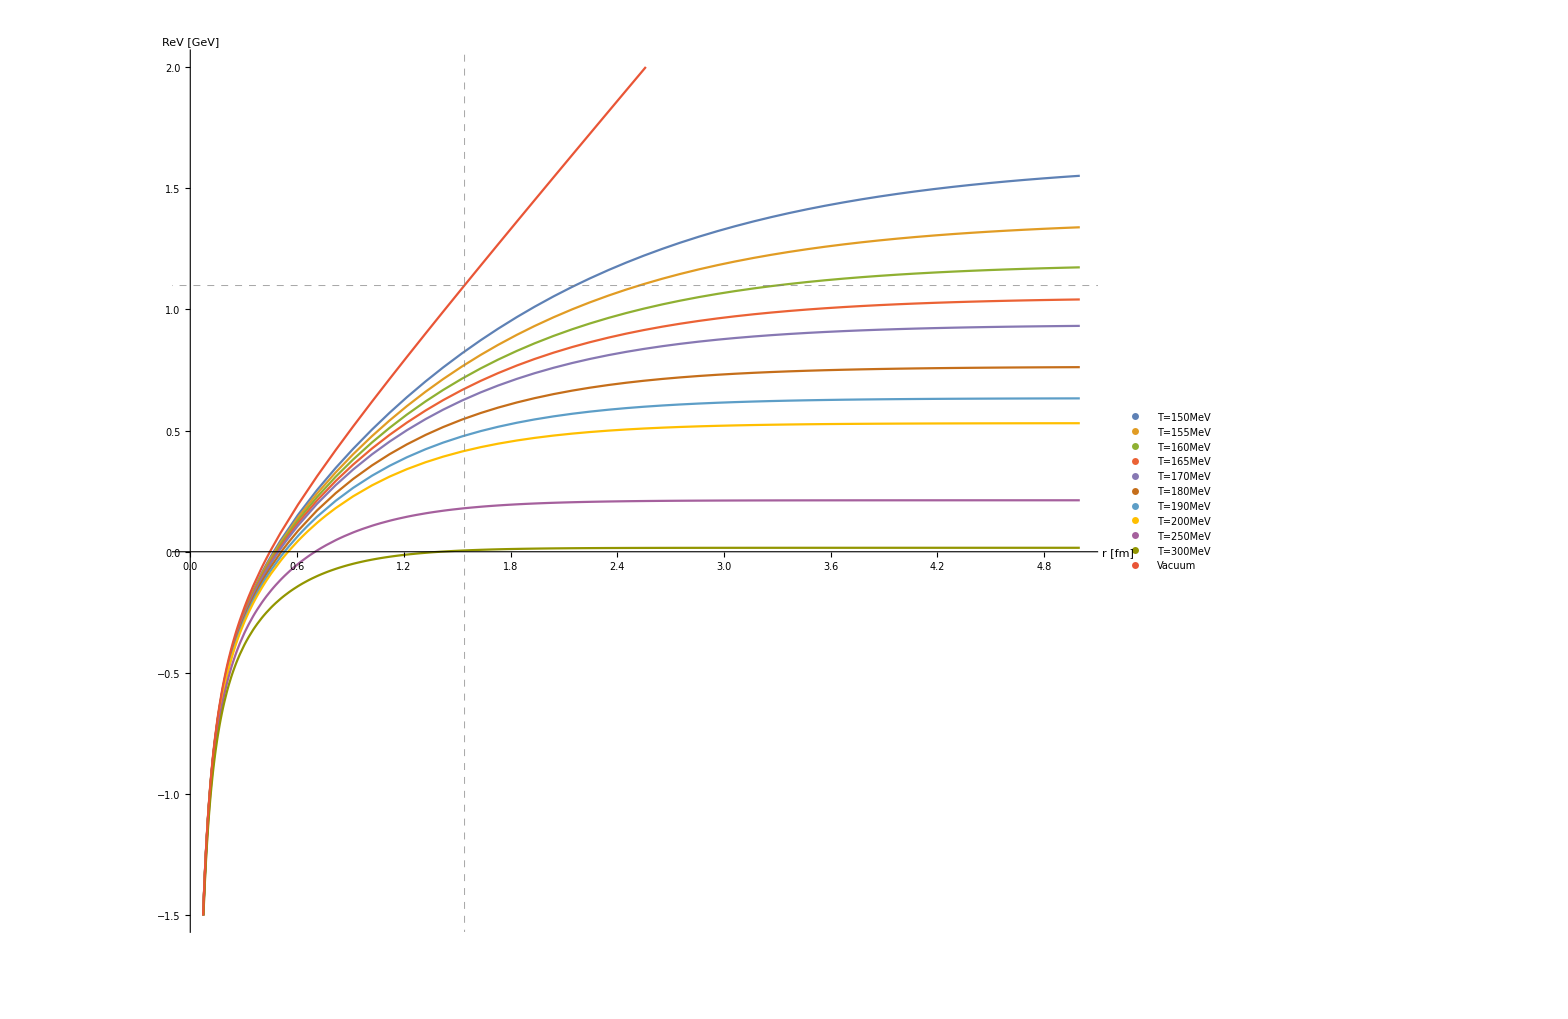

```mathematica
Plot[{ReV[r/0.197,mDcalmu[Tset[[1]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[2]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[3]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[4]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[5]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[6]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[7]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[8]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[9]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[10]],0,kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReV [GeV]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.95}],BaseStyle->{FontSize->14}]
```

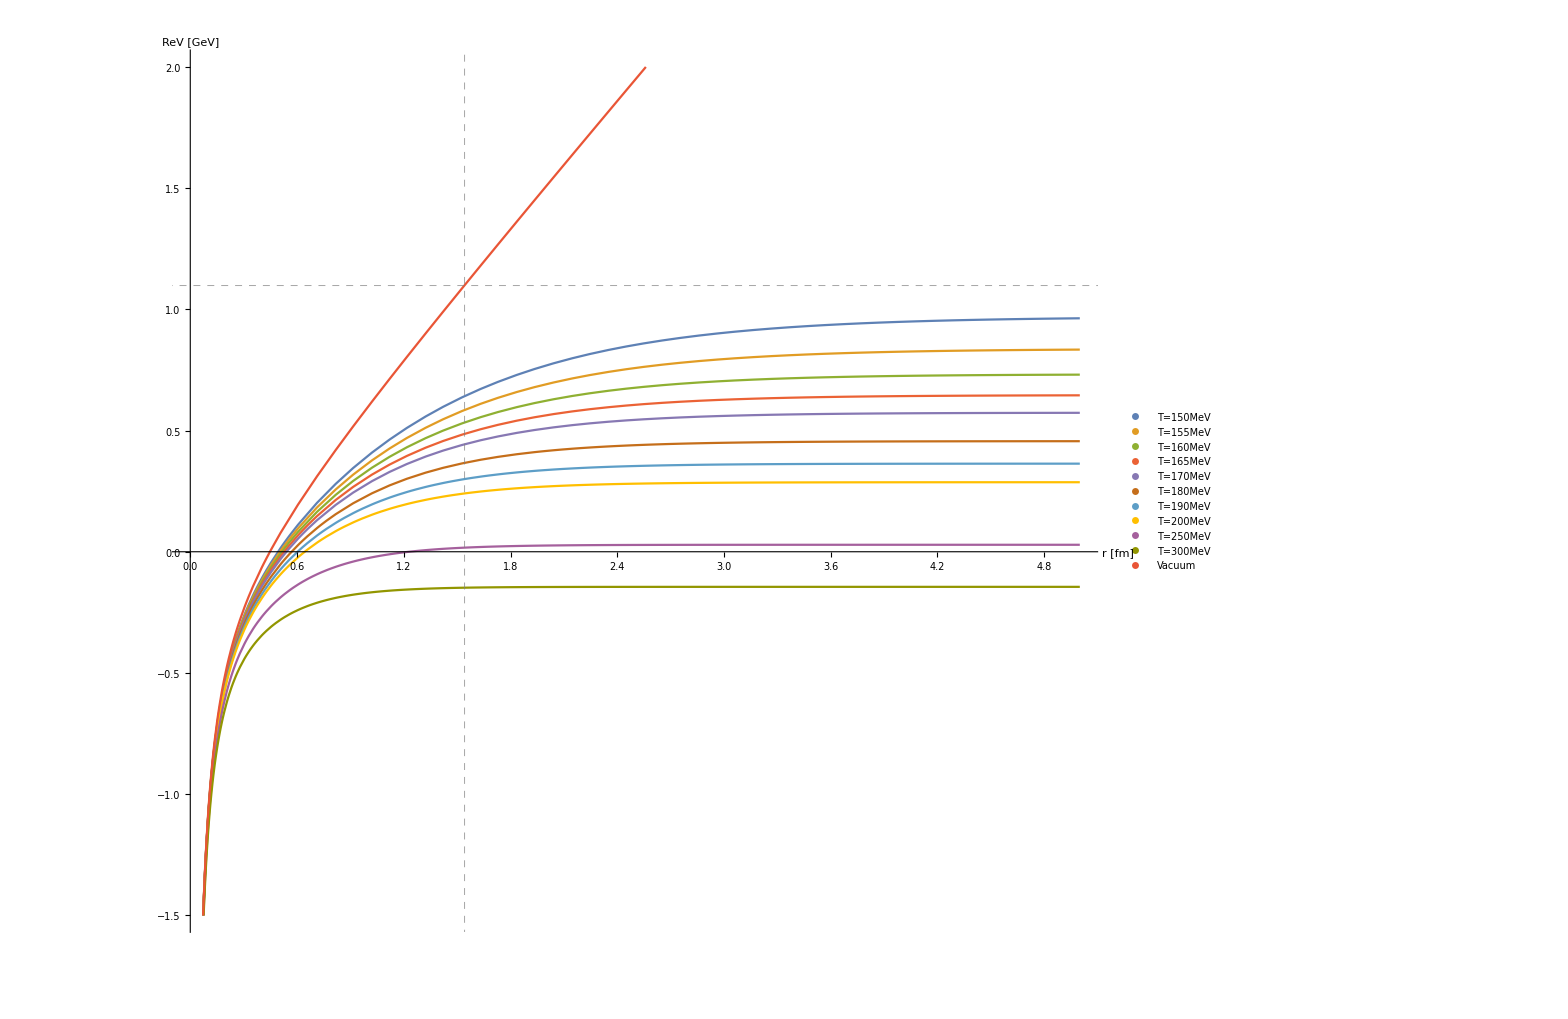

```mathematica
Plot[{ReV[r/0.197,mDcalmu[Tset[[1]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[2]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[3]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[4]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[5]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[6]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[7]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[8]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[9]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[10]],0,kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReV [GeV]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.95}],BaseStyle->{FontSize->14}]
```

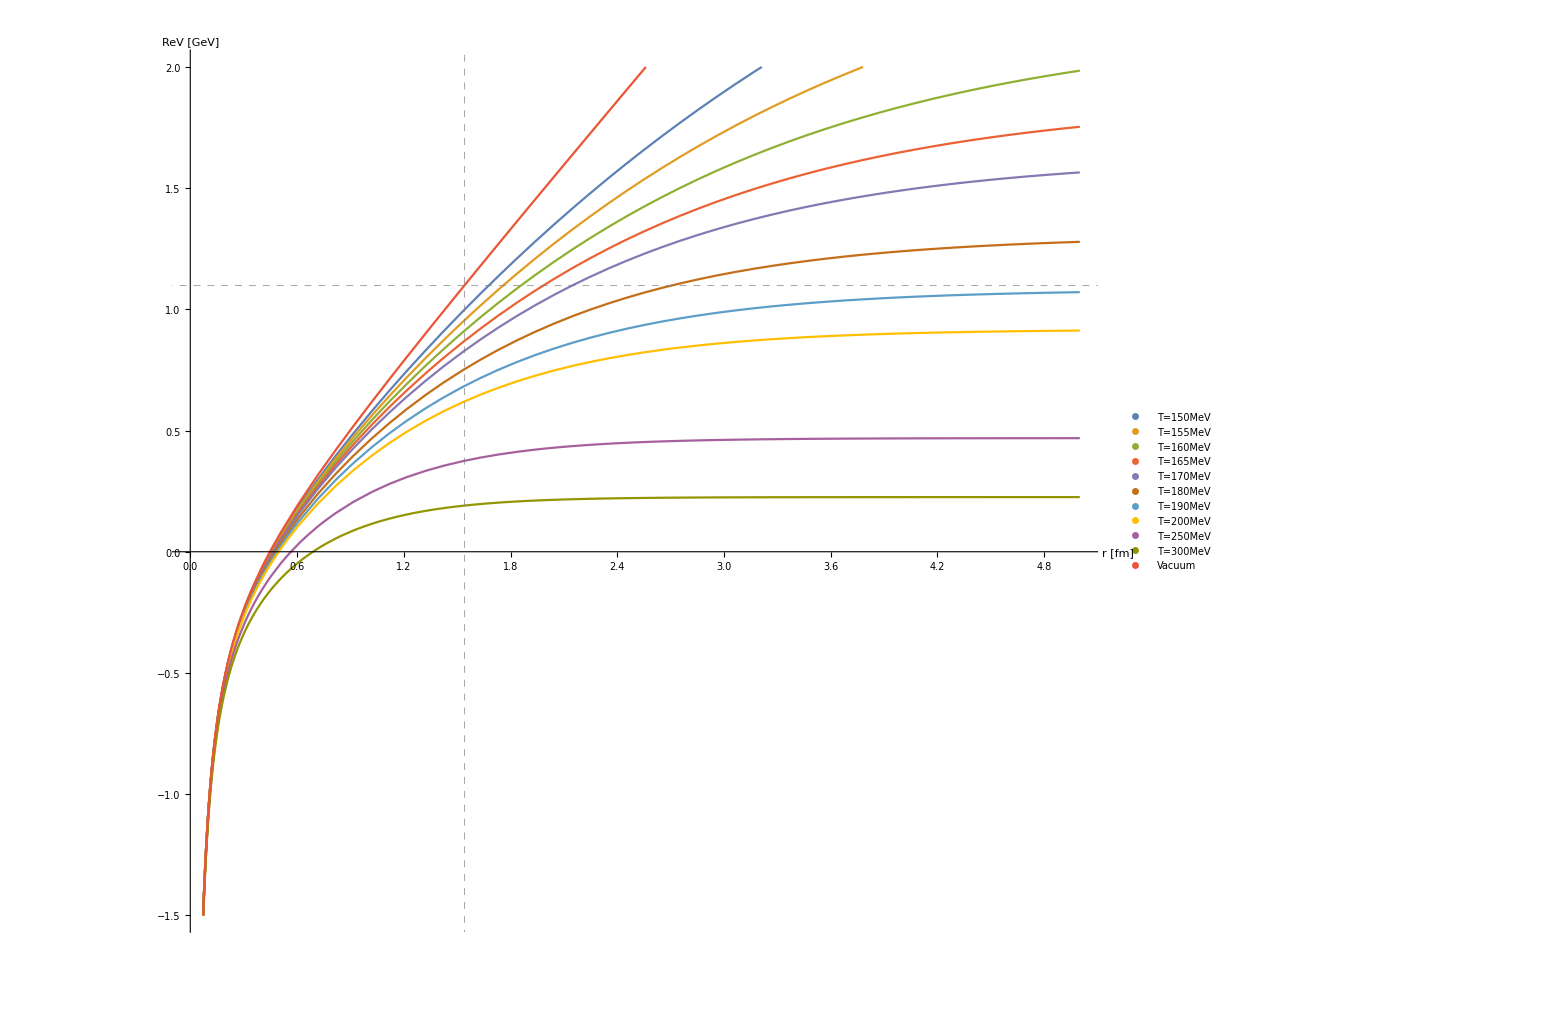

```mathematica
Plot[{ReV[r/0.197,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReV[r/0.197,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReV [GeV]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{rsbvac conv},{ReVm0[rsbvac,αcont[[1]],σcont[[1]],ccont[[1]]]}},GridLinesStyle->Directive[Gray, Dashed],PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.15}],BaseStyle->{FontSize->14}]
```

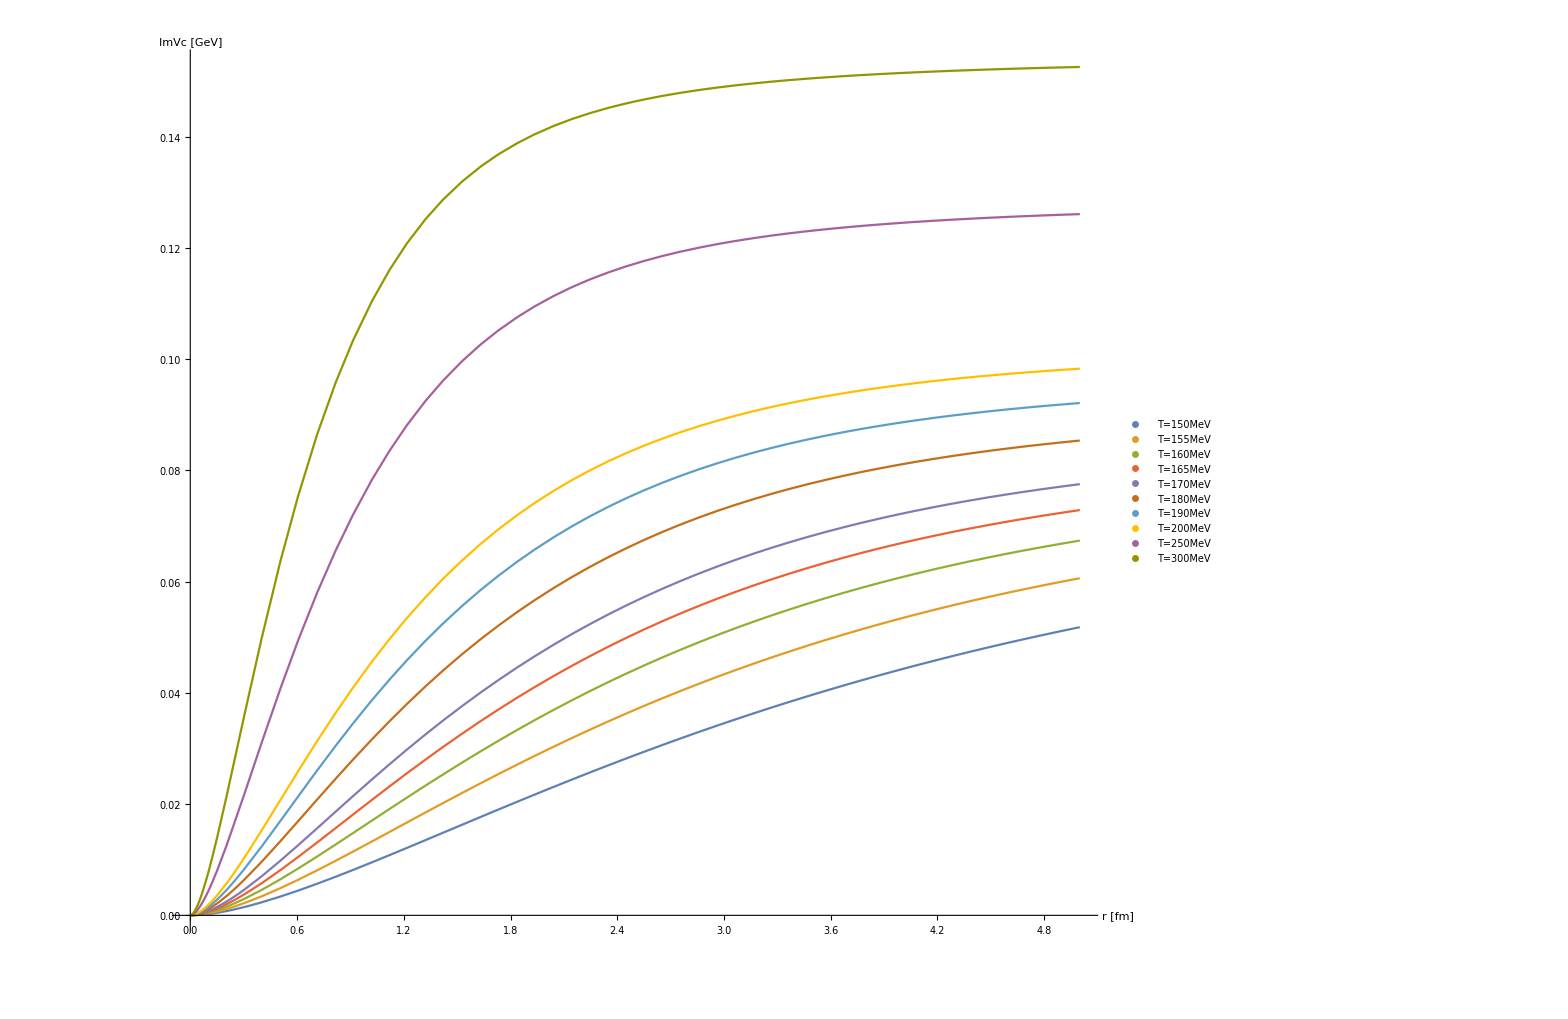

```mathematica
Plot[{ImVc[r/0.197,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[1]]],ImVc[r/0.197,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[2]]],ImVc[r/0.197,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[3]]],ImVc[r/0.197,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[4]]],ImVc[r/0.197,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[5]]],ImVc[r/0.197,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[6]]],ImVc[r/0.197,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[7]]],ImVc[r/0.197,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[8]]],ImVc[r/0.197,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[9]]],ImVc[r/0.197,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[10]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.4,0.85}]]
```

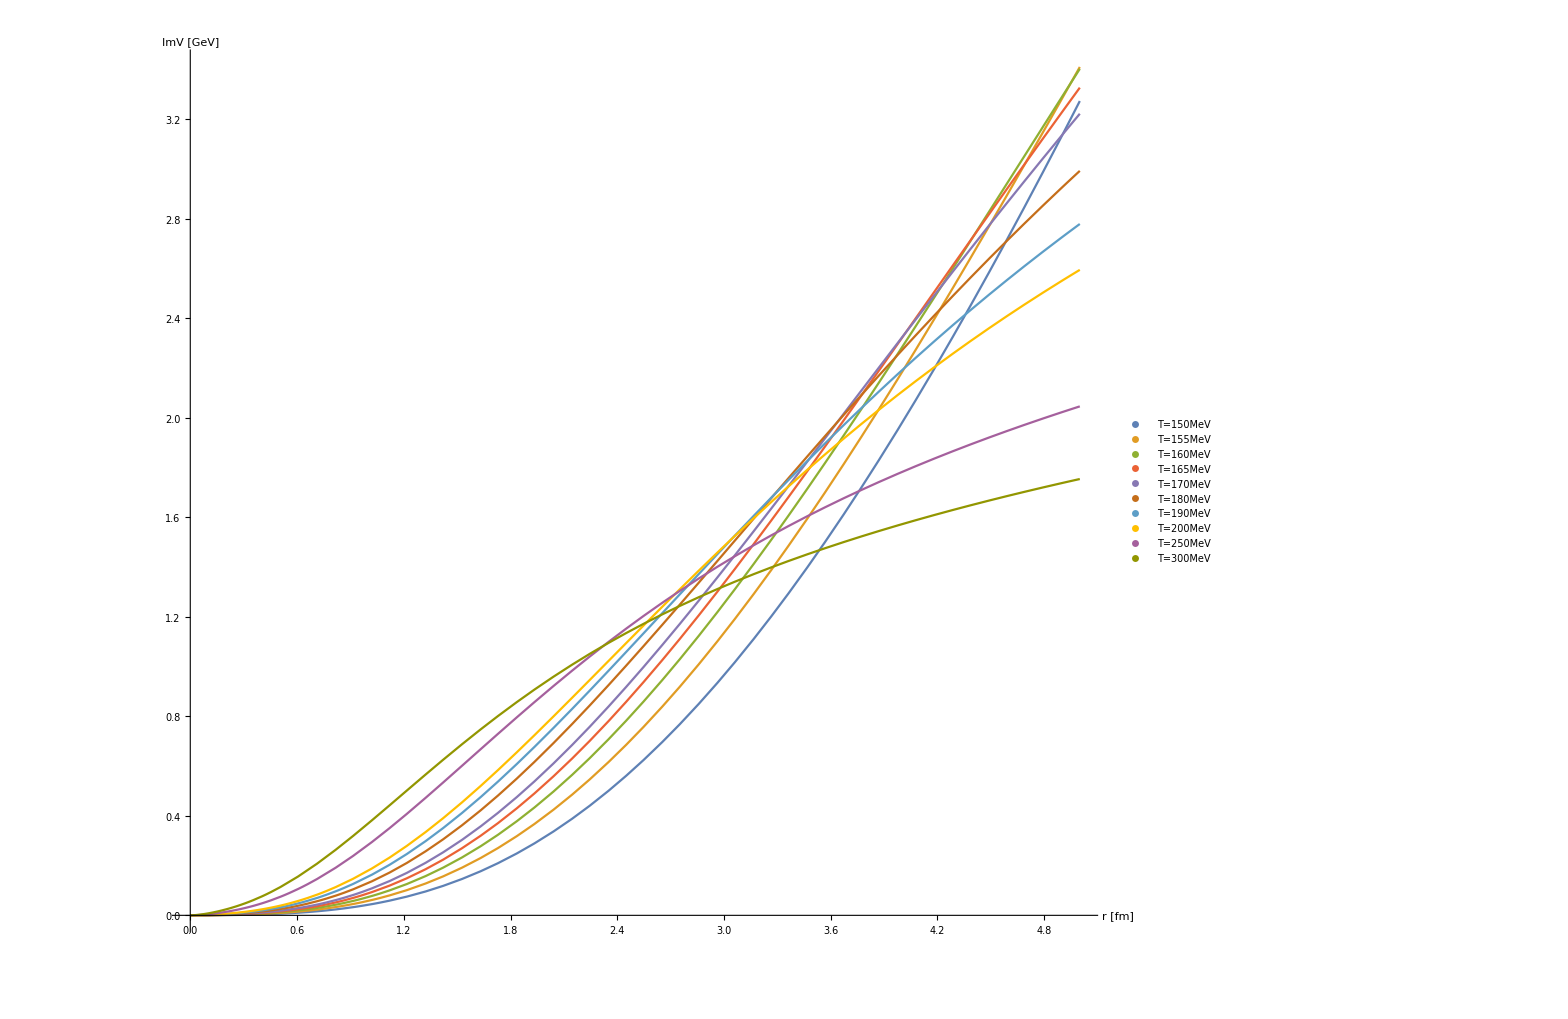

```mathematica
Plot[{ImV[r/0.197,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[1]]],ImV[r/0.197,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[2]]],ImV[r/0.197,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[3]]],ImV[r/0.197,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[4]]],ImV[r/0.197,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[5]]],ImV[r/0.197,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[6]]],ImV[r/0.197,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[7]]],ImV[r/0.197,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[8]]],ImV[r/0.197,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[9]]],ImV[r/0.197,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],Tset[[10]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImV [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.4,0.85}]]
```

### Regularisation

#### Correlation Length via Imaginary Part

```mathematica
Imrth=ConstantArray[1,Length[Tset]];
SetSharedVariable[Imrth];
ParallelDo[While[ImVc[Imrth[[l]]/conv,mDcalmu[Tset[[l]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[l]]]/(αcont[[1]]Tset[[l]])<990/1000,Imrth[[l]]=Imrth[[l]]+1],{l,Length[Imrth]}];//AbsoluteTiming
```

{5.93929,Null}

```mathematica
Imrth=9/10 Imrth;
ParallelDo[While[ImVc[Imrth[[l]]/conv,mDcalmu[Tset[[l]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[l]]]/(αcont[[1]]Tset[[l]])<990/1000,Imrth[[l]]=Imrth[[l]]+1/100],{l,Length[Imrth]}];//AbsoluteTiming
```

{23.7196,Null}

```mathematica
Imrth=95/100 Imrth;
ParallelDo[While[ImVc[Imrth[[l]]/conv,mDcalmu[Tset[[l]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[l]]]/(αcont[[1]]Tset[[l]])<990/1000,Imrth[[l]]=Imrth[[l]]+1/1000],{l,Length[Imrth]}];//AbsoluteTiming
```

{156.723,Null}

```mathematica
N[Imrth]
```

{29.556,20.0605,17.539,15.6845,13.118,11.4035,10.1635,6.9675,5.4295}

```mathematica
reg=ConstantArray[1/1000,Length[Imrth]];
SetSharedVariable[reg];
ParallelDo[While[ImVsr[Imrth[[l]]/conv,mDcalmu[Tset[[l]],0,kfinall[[1]],kfinall[[2]]],reg[[l]],σcont[[1]],Tset[[l]]]/ImVsAs[mDcalmu[Tset[[l]],0,kfinall[[1]],kfinall[[2]]],reg[[l]],σcont[[1]],Tset[[l]]]<990/1000,reg[[l]]=reg[[l]]+1/100],{l,Length[reg]}];
```

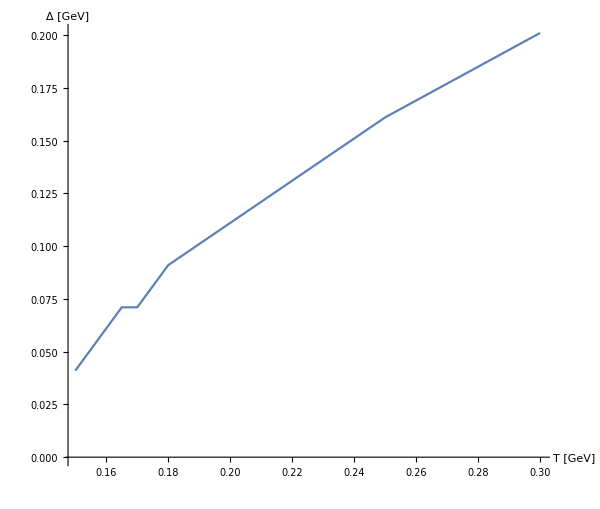

```mathematica
ListPlot[Transpose[{Tset,reg}],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Δ [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

```mathematica
ImVsAll[n1_]:=Block[{n=n1,temp},temp=ImVsTab[mDcalmu[Tset[[n]],0,kfinall[[1]],kfinall[[2]]],reg[[n]],σcont[[1]],Tset[[n]]];
Export["reg_pot/ImVsT"<>ToString[n]<>".dat",temp];
ImVsInter[n]=Interpolation[temp];]
```

```mathematica
ImVsAll[1]//AbsoluteTiming
```

```mathematica
ImVsAll[2]//AbsoluteTiming
```

{264.338,Null}

```mathematica
ImVsAll[3]//AbsoluteTiming
```

{269.059,Null}

```mathematica
ImVsAll[4]//AbsoluteTiming
```

{275.848,Null}

```mathematica
ImVsAll[5]//AbsoluteTiming
```

{299.729,Null}

```mathematica
ImVsAll[6]//AbsoluteTiming
```

{312.799,Null}

```mathematica
ImVsAll[7]//AbsoluteTiming
```

{317.583,Null}

```mathematica
ImVsAll[8]//AbsoluteTiming
```

{345.923,Null}

```mathematica
ImVsAll[9]//AbsoluteTiming
```

{303.113,Null}

```mathematica
ImVsInter[1]=Interpolation[ToExpression[Import["reg_pot/ImVsT1.dat"]]];
ImVsInter[2]=Interpolation[ToExpression[Import["reg_pot/ImVsT2.dat"]]];
ImVsInter[3]=Interpolation[ToExpression[Import["reg_pot/ImVsT3.dat"]]];
ImVsInter[4]=Interpolation[ToExpression[Import["reg_pot/ImVsT4.dat"]]];
ImVsInter[5]=Interpolation[ToExpression[Import["reg_pot/ImVsT5.dat"]]];
ImVsInter[6]=Interpolation[ToExpression[Import["reg_pot/ImVsT6.dat"]]];
ImVsInter[7]=Interpolation[ToExpression[Import["reg_pot/ImVsT7.dat"]]];
ImVsInter[8]=Interpolation[ToExpression[Import["reg_pot/ImVsT8.dat"]]];
ImVsInter[9]=Interpolation[ToExpression[Import["reg_pot/ImVsT9.dat"]]];
```

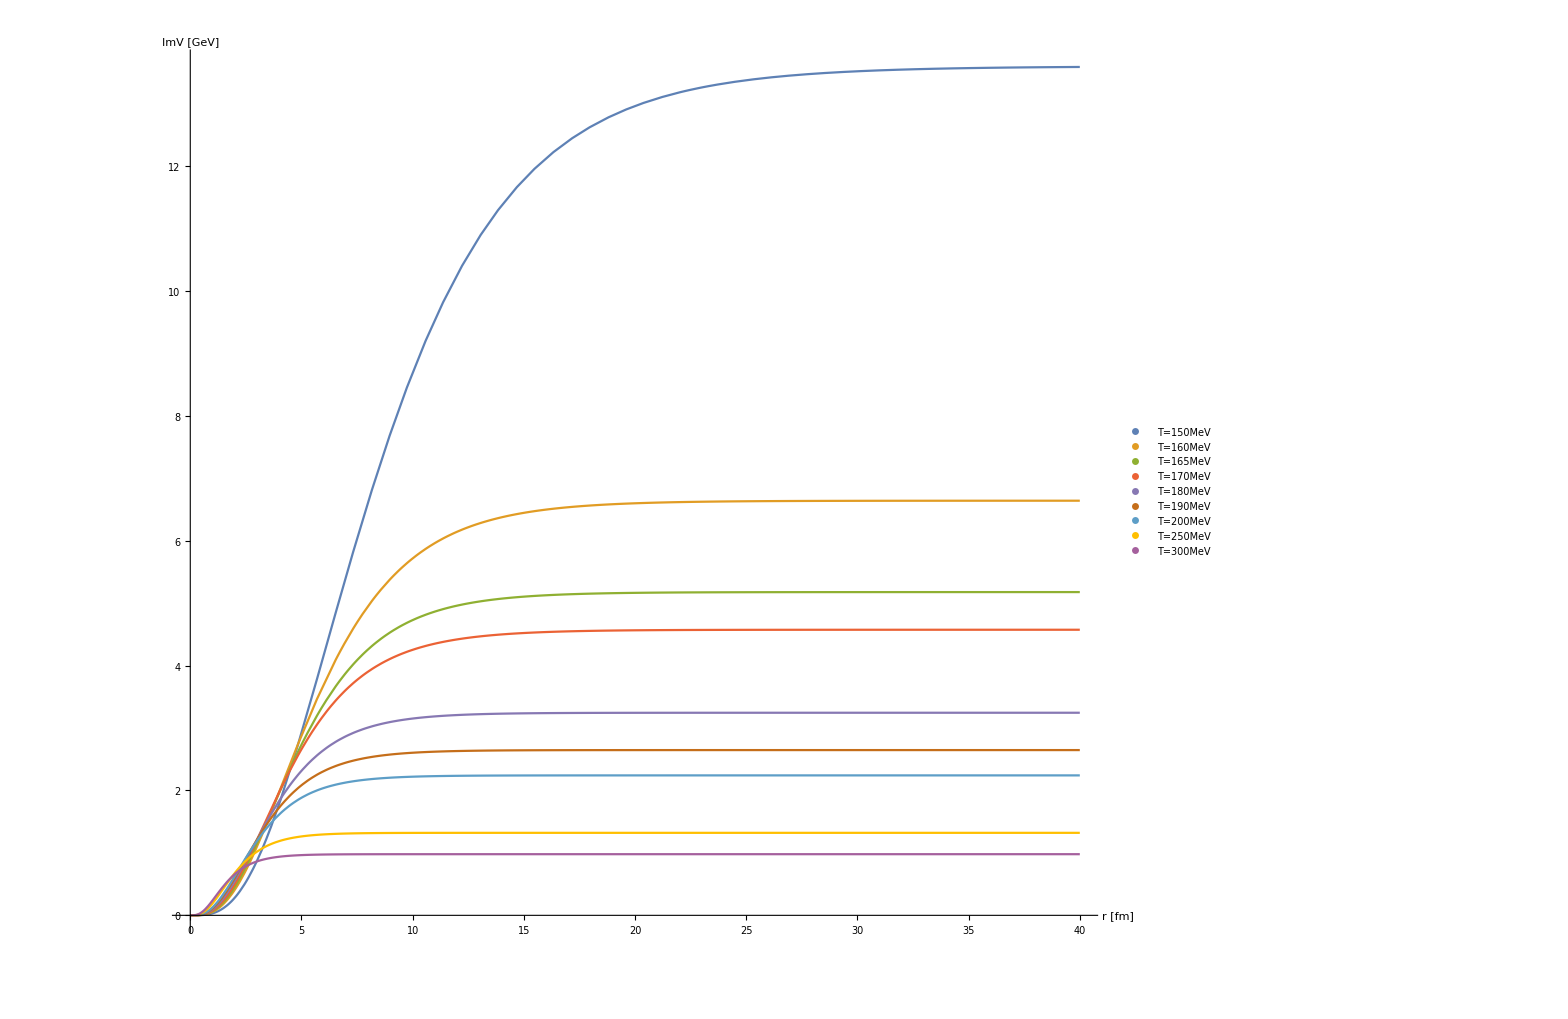

```mathematica
Plot[{ImVsInter[1][x/conv],ImVsInter[2][x/conv],ImVsInter[3][x/conv],ImVsInter[4][x/conv],ImVsInter[5][x/conv],ImVsInter[6][x/conv],ImVsInter[7][x/conv],ImVsInter[8][x/conv],ImVsInter[9][x/conv]},{x,0,40},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImV [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.6,0.7}]]
```

#### Correlation Length via Real Part

```mathematica
ReVas[s_]:=Block[{an=ccont[[1]]-αcont[[1]]mDcal[2π,Tset[[s]],kfinal[[1]],kfinal[[2]]]+(2 σcont[[1]])/mDcal[2π,Tset[[s]],kfinal[[1]],kfinal[[2]]]},If[an>0,0.999an,1.001 an]];
ReVlas[s_]:=Block[{an=ccont[[1]]-αcont[[1]]mDcal[2π,Tset[[s]],kfinall[[1]],kfinall[[2]]]+(2 σcont[[1]])/mDcal[2π,Tset[[s]],kfinall[[1]],kfinall[[2]]]},If[an>0,0.999an,1.001 an]];
ReVuas[s_]:=Block[{an=ccont[[1]]-αcont[[1]]mDcal[2π,Tset[[s]],kfinalu[[1]],kfinalu[[2]]]+(2 σcont[[1]])/mDcal[2π,Tset[[s]],kfinalu[[1]],kfinalu[[2]]]},If[an>0,0.999an,1.001 an]];
```

```mathematica
rth=Table[{Tset[[n]], r/.FindRoot[ReV[r/conv,mDcal[2π,Tset[[n]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==ReVas[n],{r,1,1/100,20}]},{n,1,Length[Tset]}];
rthsb=rth;
Do[If[ReV[rthsb[[n,2]]/conv,mDcal[2π,Tset[[n]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]>11/10,rthsb[[n,2]]=r/.FindRoot[ReV[r/conv,mDcal[2π,Tset[[n]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==1.1,{r,1,1/100,20}]],{n,Length[rthsb]}];
rth=SetPrecision[rth,30];
rthsb=SetPrecision[rthsb,30];
```

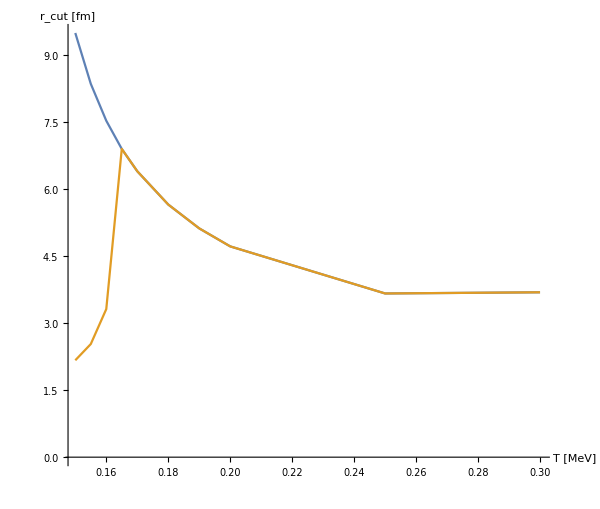

```mathematica
ListPlot[{rth,rthsb},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","r_cut [fm]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

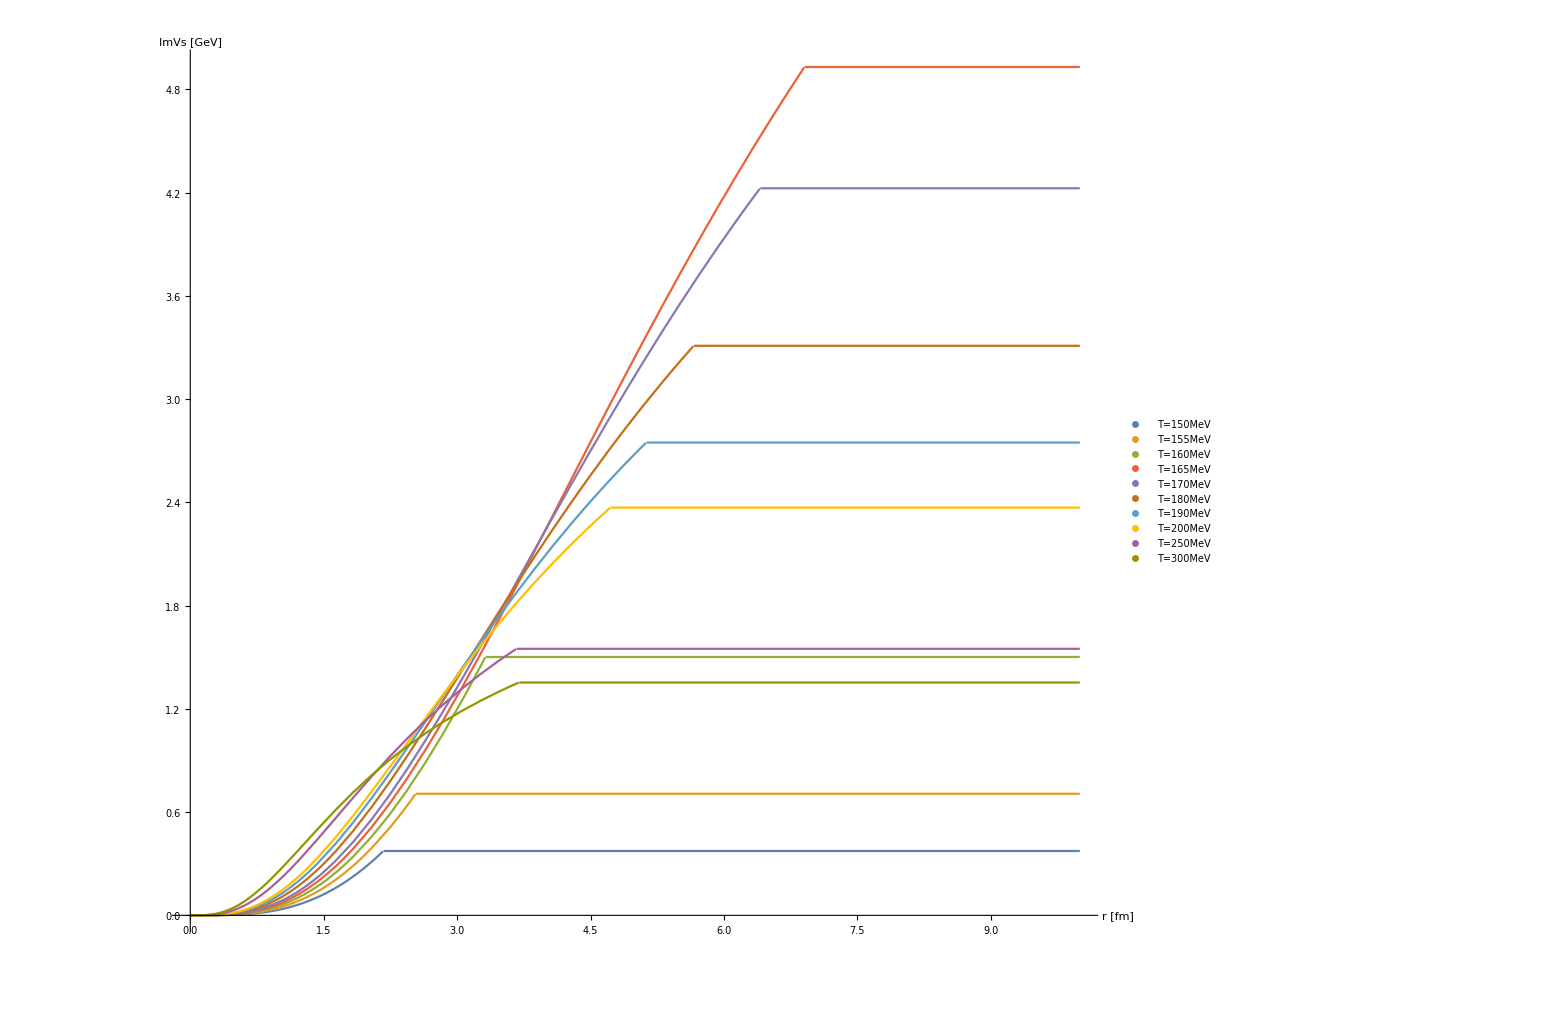

```mathematica
Plot[{ImVssb[r/conv,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[1]],rth[[1,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[2]],rth[[2,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[3]],rth[[3,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[4]],rth[[4,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[5]],rth[[5,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[6]],rth[[6,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[7]],rth[[7,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[8]],rth[[8,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[9]],rth[[9,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[10]],rth[[10,2]]/conv]},{r,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.4,0.85}]]
```

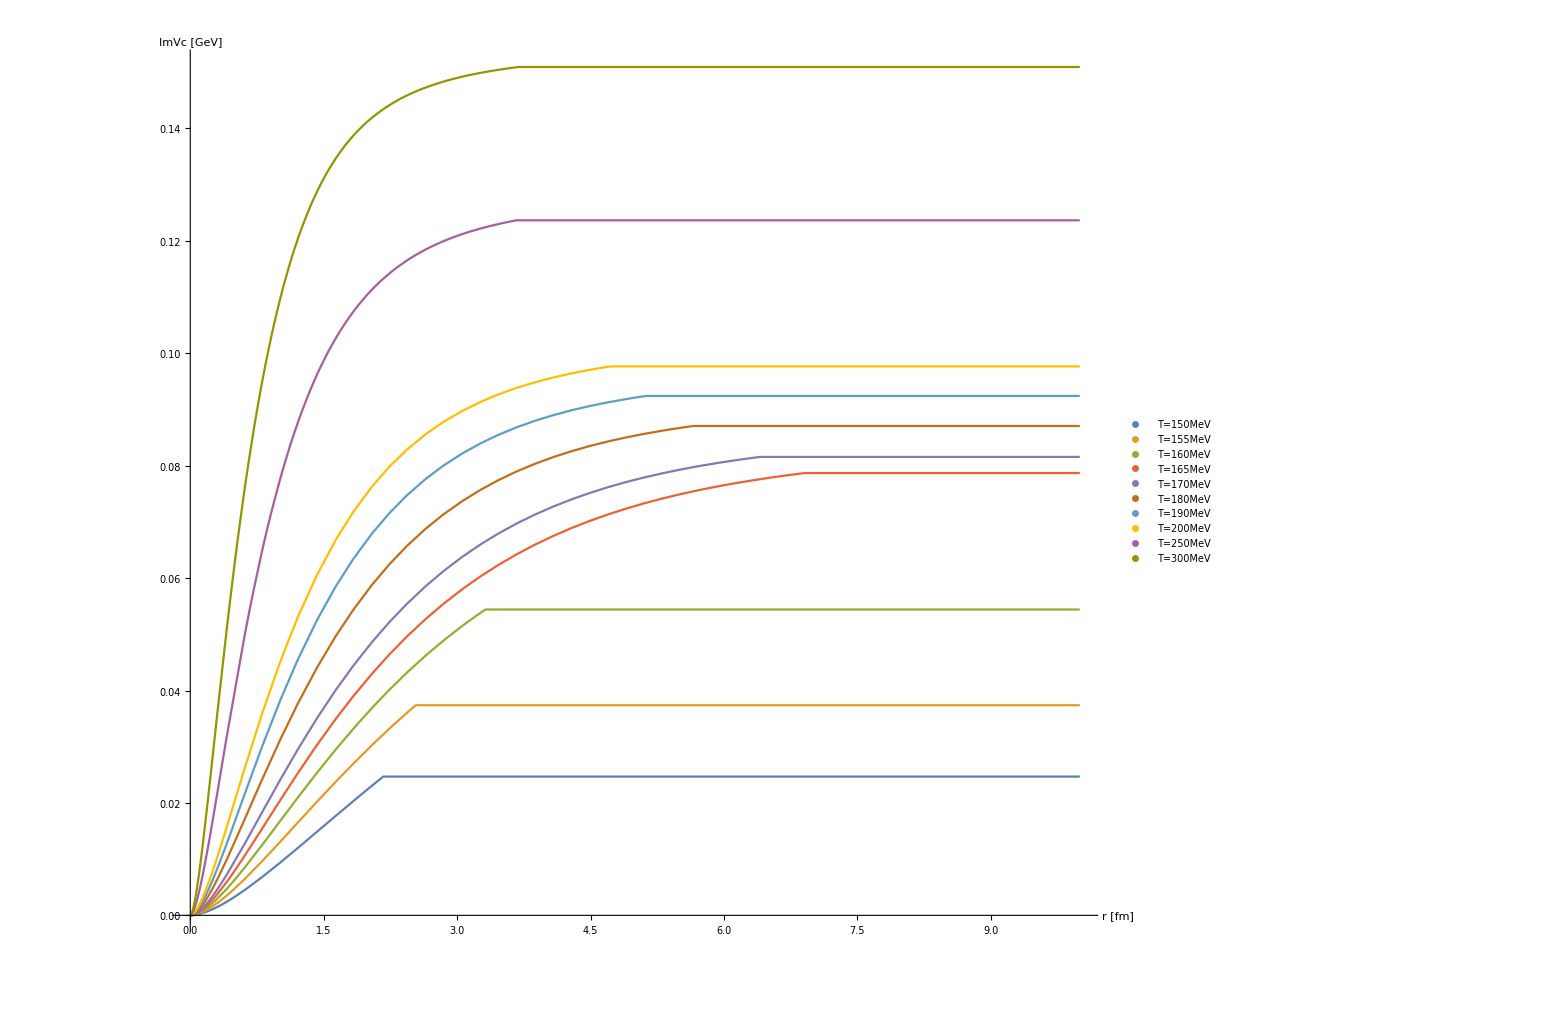

```mathematica
Plot[{ImVcsb[r/conv,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[1]],rth[[1,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[2]],rth[[2,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[3]],rth[[3,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[4]],rth[[4,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[5]],rth[[5,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[6]],rth[[6,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[7]],rth[[7,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[8]],rth[[8,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[9]],rth[[9,2]]/conv],ImVcsb[r/conv,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[10]],rth[[10,2]]/conv]},{r,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.4,0.85}]]
```

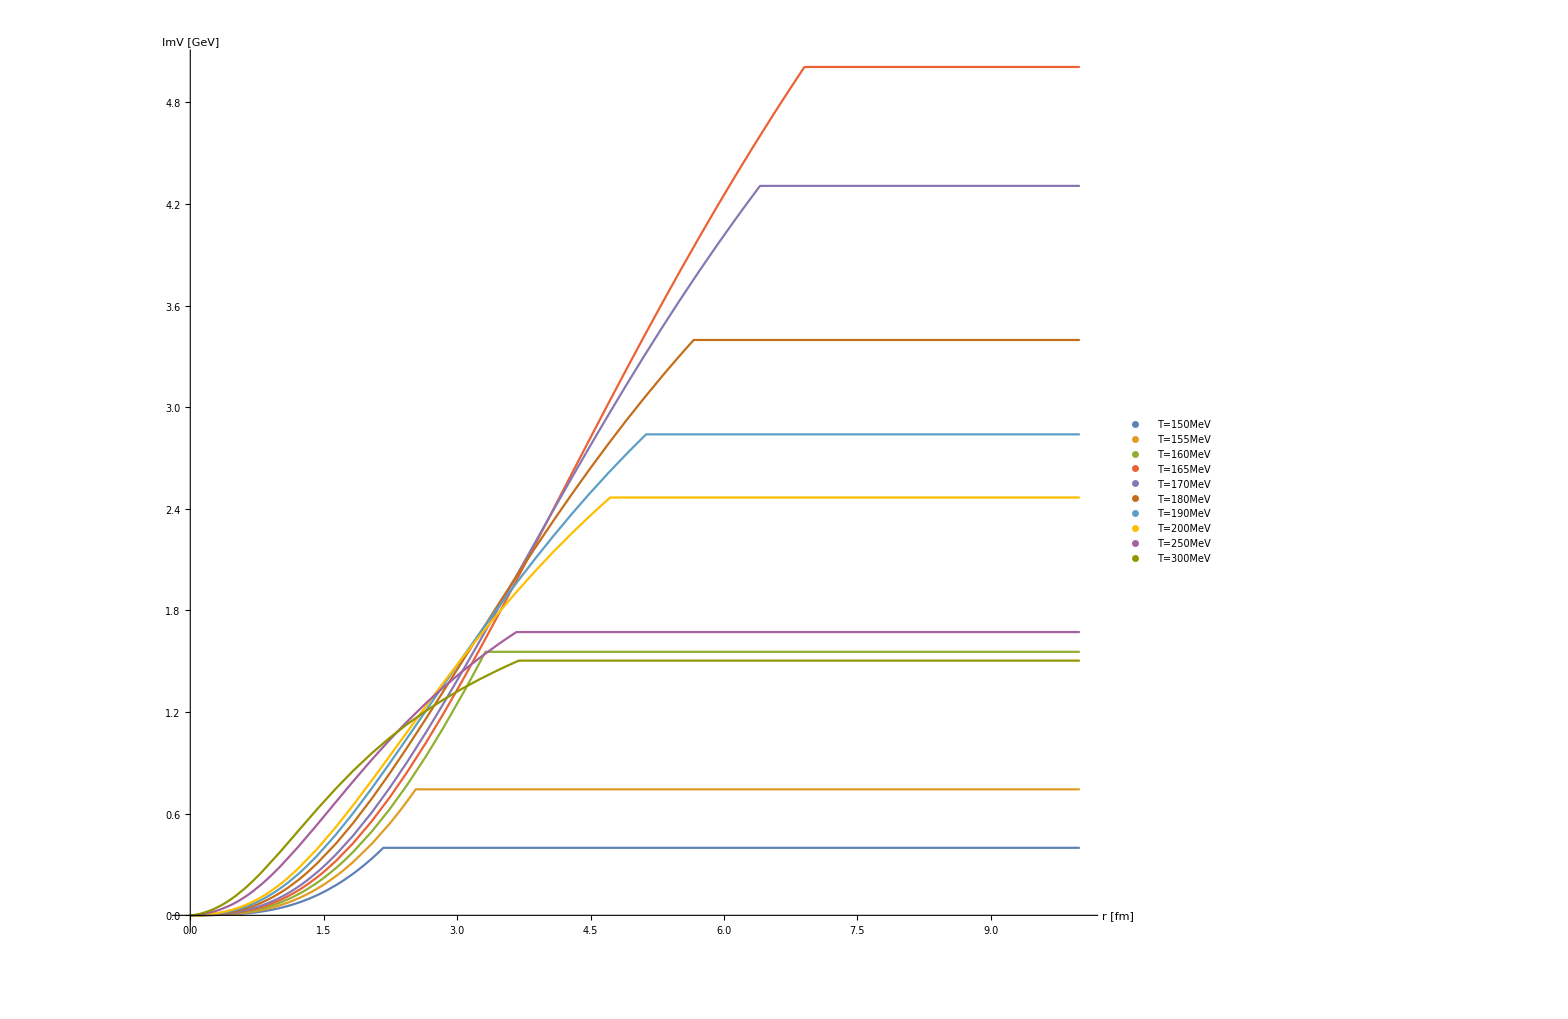

```mathematica
Plot[{ImVssb[r/conv,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[1]],rth[[1,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[1]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[1]],rth[[1,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[2]],rth[[2,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[2]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[2]],rth[[2,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[3]],rth[[3,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[3]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[3]],rth[[3,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[4]],rth[[4,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[4]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[4]],rth[[4,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[5]],rth[[5,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[5]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[5]],rth[[5,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[6]],rth[[6,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[6]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[6]],rth[[6,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[7]],rth[[7,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[7]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[7]],rth[[7,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[8]],rth[[8,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[8]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[8]],rth[[8,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[9]],rth[[9,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[9]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[9]],rth[[9,2]]/conv],ImVssb[r/conv,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],σcont[[1]],Tset[[10]],rth[[10,2]]/conv]+ImVcsb[r/conv,mDcalmu[Tset[[10]],0,kfinall[[1]],kfinall[[2]]],αcont[[1]],Tset[[10]],rth[[10,2]]/conv]},{r,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImV [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.4,0.85}]]
```

```mathematica
regre=ConstantArray[1/1000,Length[rth]];
SetSharedVariable[regre];
ParallelDo[While[ImVsr[rth[[l,2]]/conv,mDcal[2π,Tset[[l]],kfinal[[1]],kfinal[[2]]],regre[[l]],σcont[[1]],Tset[[l]]]/ImVsAs[mDcal[2π,Tset[[l]],kfinal[[1]],kfinal[[2]]],regre[[l]],σcont[[1]],Tset[[l]]]<990/1000,regre[[l]]=regre[[l]]+1/1000],{l,Length[regre]}];
```

```mathematica
regre=SetPrecision[{0.292,0.316,0.336,0.352,0.366,0.387,0.403,0.414,0.424,0.317},30];
```

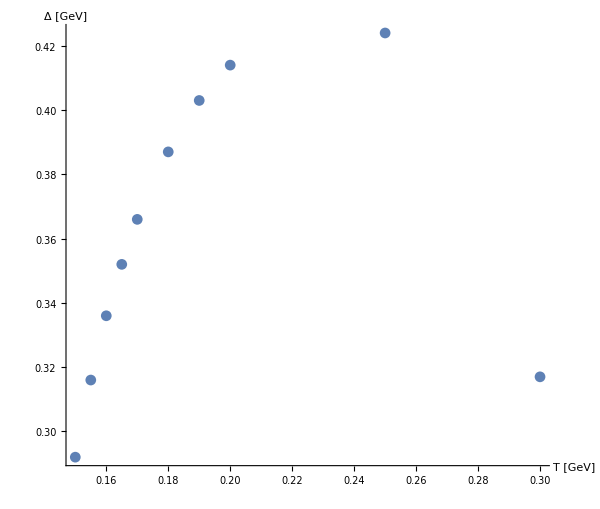

```mathematica
ListPlot[Transpose[{Tset,regre}],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Δ [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

```mathematica
ImVsAll[n1_]:=Block[{n=n1,temp},temp=ImVsTab[mDcal[2π,Tset[[n]],kfinal[[1]],kfinal[[2]]],regre[[n]],σcont[[1]],Tset[[n]]];
Export["reg_pot/ImVsT"<>ToString[n]<>".dat",temp];
ImVsInter[n]=Interpolation[temp];]
```

```mathematica
TsetSnew={"T=150MeV","T=155MeV","T=160MeV","T=165MeV","T=170MeV","T=180MeV","T=190MeV","T=200MeV","T=250MeV"};
```

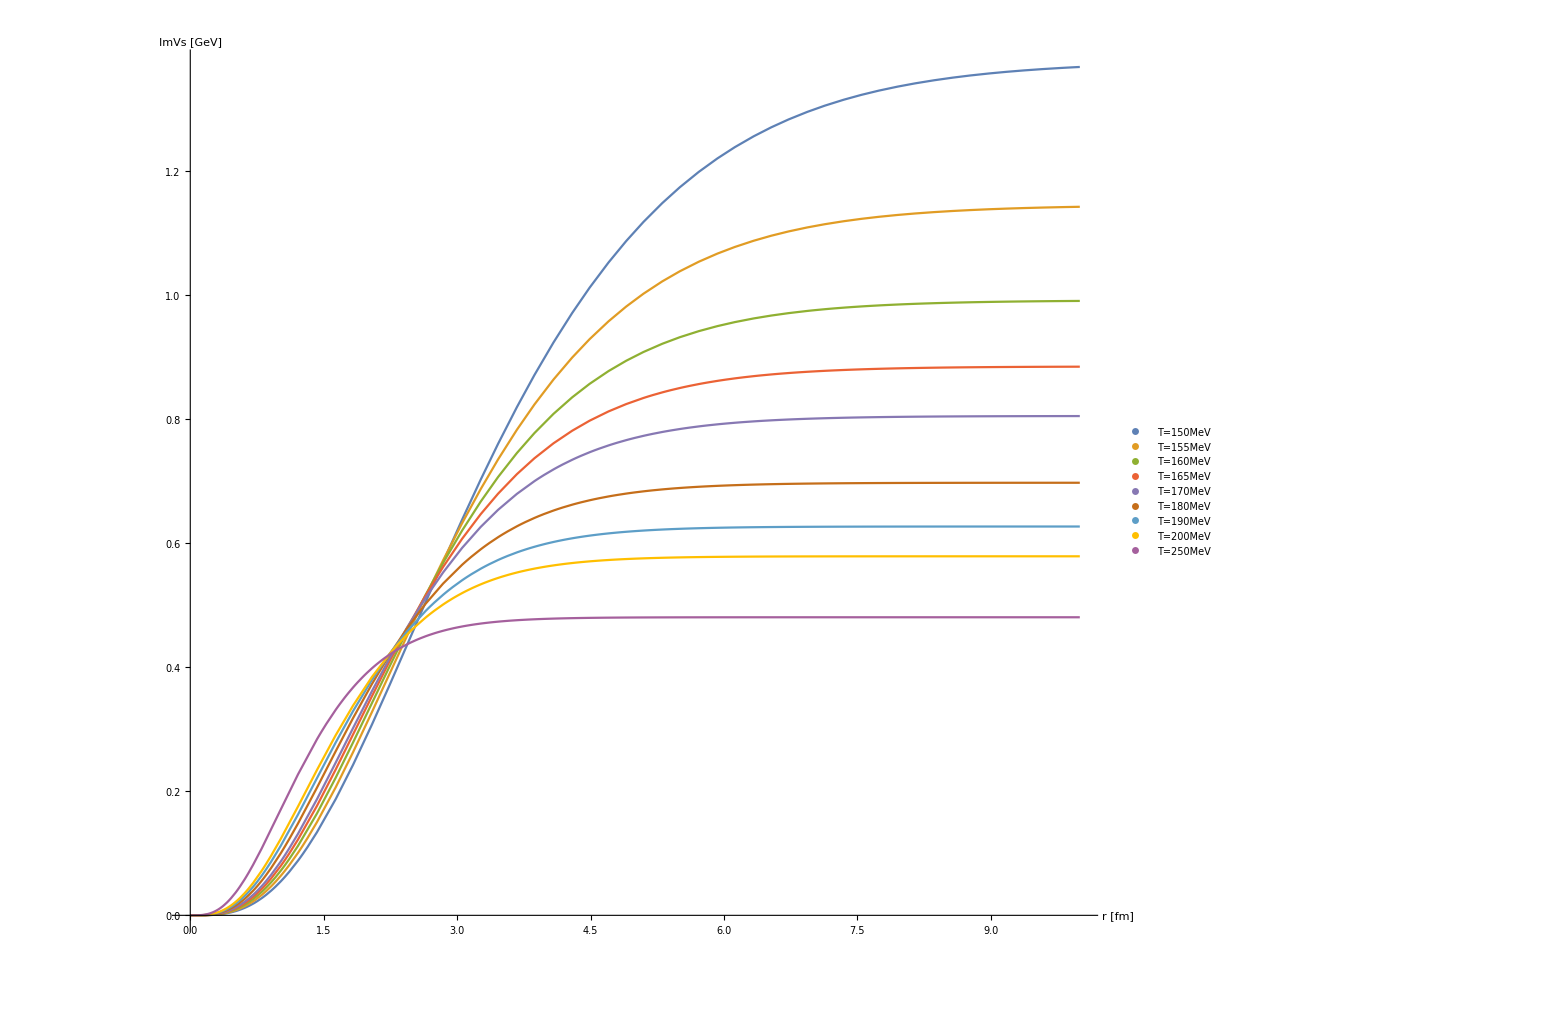

```mathematica
Plot[{ImVsInter[1][x/conv],ImVsInter[2][x/conv],ImVsInter[3][x/conv],ImVsInter[4][x/conv],ImVsInter[5][x/conv],ImVsInter[6][x/conv],ImVsInter[7][x/conv],ImVsInter[8][x/conv],ImVsInter[9][x/conv]},{x,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetSnew, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.3,0.9}]]
```

```mathematica
N[Tset]
```

{0.15,0.155,0.16,0.165,0.17,0.18,0.19,0.2,0.25,0.3}

```mathematica
N[rthsb]
```

{{0.15,2.17023},{0.155,2.53405},{0.16,3.31746},{0.165,6.90512},{0.17,6.40528},{0.18,5.65923},{0.19,5.12506},{0.2,4.72173},{0.25,3.66693},{0.3,3.69353}}

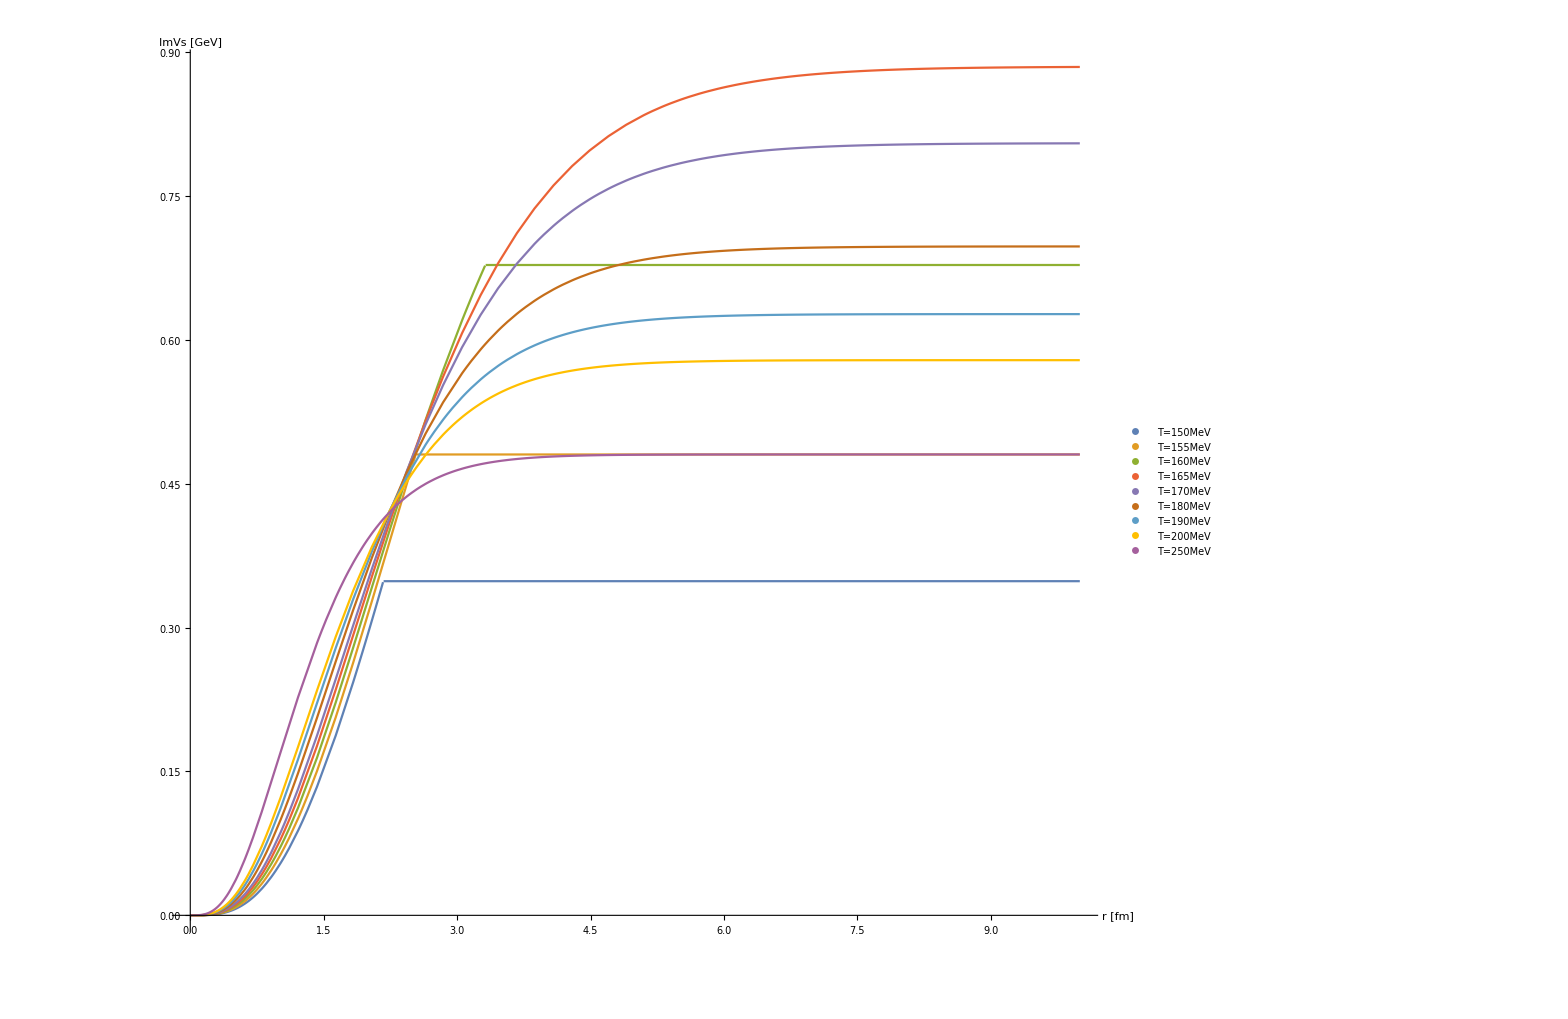

```mathematica
Plot[{Piecewise[{{ImVsInter[1][x/conv],x<rthsb[[1,2]]},{ImVsInter[1][rthsb[[1,2]]/conv],x≥rthsb[[1,2]]}}],Piecewise[{{ImVsInter[2][x/conv],x<rthsb[[2,2]]},{ImVsInter[2][rthsb[[2,2]]/conv],x≥rthsb[[2,2]]}}],Piecewise[{{ImVsInter[3][x/conv],x<rthsb[[3,2]]},{ImVsInter[3][rthsb[[3,2]]/conv],x≥rthsb[[3,2]]}}],ImVsInter[4][x/conv],ImVsInter[5][x/conv],ImVsInter[6][x/conv],ImVsInter[7][x/conv],ImVsInter[8][x/conv],ImVsInter[9][x/conv]},{x,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetSnew, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.25,0.9}]]
```

```mathematica
rthu=Table[{Tset[[n]], r/.FindRoot[ReV[r/conv,mDcal[2π,Tset[[n]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==ReVuas[n],{r,1,1/100,10}]},{n,1,Length[Tset]}];
rthsbu=rthu;
Do[If[ReV[rthsbu[[n,2]]/conv,mDcal[2π,Tset[[n]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]>11/10,rthsbu[[n,2]]=r/.FindRoot[ReV[r/conv,mDcal[2π,Tset[[n]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==1.1,{r,1,1/100,20}]],{n,Length[rthsbu]}];
rthu=SetPrecision[rth,30];
rthsbu=SetPrecision[rthsb,30];
```

```mathematica
rthl=Table[{Tset[[n]], r/.FindRoot[ReV[r/conv,mDcal[2π,Tset[[n]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==ReVlas[n],{r,1,1/100,20}]},{n,1,Length[Tset]}];
rthsbl=rthl;
Do[If[ReV[rthsbl[[n,2]]/conv,mDcal[2π,Tset[[n]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]>11/10,rthsbl[[n,2]]=r/.FindRoot[ReV[r/conv,mDcal[2π,Tset[[n]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]]==1.1,{r,1,1/100,20}]],{n,Length[rthsbl]}];
rthl=SetPrecision[rth,30];
rthsbl=SetPrecision[rthsb,30];
```

#### Via hyperbolic tangent

```mathematica
N[rth]
```

{{0.15,9.50219},{0.155,8.36336},{0.16,7.53635},{0.165,6.90512},{0.17,6.40528},{0.18,5.65923},{0.19,5.12506},{0.2,4.72173},{0.25,3.66693},{0.3,3.69353}}

```mathematica
N[rthsb]
```

{{0.15,2.17023},{0.155,2.53405},{0.16,3.31746},{0.165,6.90512},{0.17,6.40528},{0.18,5.65923},{0.19,5.12506},{0.2,4.72173},{0.25,3.66693},{0.3,3.69353}}

```mathematica
ImVsARTab[mD1_,Δ1_,σ1_,T1_]:=Block[{mD=mD1,Δ=Δ1,σ=σ1,T=T1},Join[{{0,0}},ParallelTable[{r,NIntegrate[(2 mD^2 T σ (2-2 Cos[p r]-p r Sin[p r]))/(p(mD^2+p^2)^2)Tanh[Δ p],{p,0,∞},WorkingPrecision->20,MaxRecursion->20]},{r,1/100,100,1/100}]]];
ImVsARAs[mD_,Δ_,σ_,T_]:=4 mD^2 T σ NIntegrate[1/(p(mD^2+p^2)^2)Tanh[Δ^-1 p],{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
ImVsrAR[r_,mD_,Δ_,σ_,T_]:=2 mD^2 T σ NIntegrate[(2-2 Cos[p r]-p r Sin[p r])/(p(mD^2+p^2)^2)Tanh[Δ^-1 p],{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
```

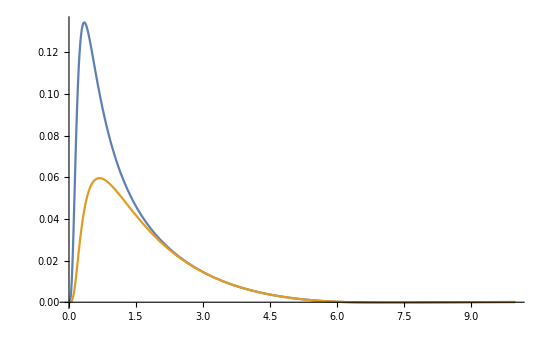

```mathematica
Block[{mD=0.2,r=1,Δ=1},Plot[{(2-2 Cos[p r]-p r Sin[p r])/(p(mD^2+p^2)^2),(2-2 Cos[p r]-p r Sin[p r])/(p(mD^2+p^2)^2)Tanh[p/Δ]},{p,0,10},PlotRange->All]]
```

```mathematica
regARre=ConstantArray[1/1000,Length[rth]];
SetSharedVariable[regARre];
ParallelDo[While[ImVsrAR[rth[[l,2]]/conv,mDcal[2π,Tset[[l]],kfinal[[1]],kfinal[[2]]],regARre[[l]],σcont[[1]],Tset[[l]]]/ImVsARAs[mDcal[2π,Tset[[l]],kfinal[[1]],kfinal[[2]]],regARre[[l]],σcont[[1]],Tset[[l]]]<990/1000,regARre[[l]]=regARre[[l]]+1/1000],{l,Length[regARre]}];
```

```mathematica
regARre={0.237,0.256,0.272,0.285,0.295,0.312,0.323,0.332,0.337,0.252};
```

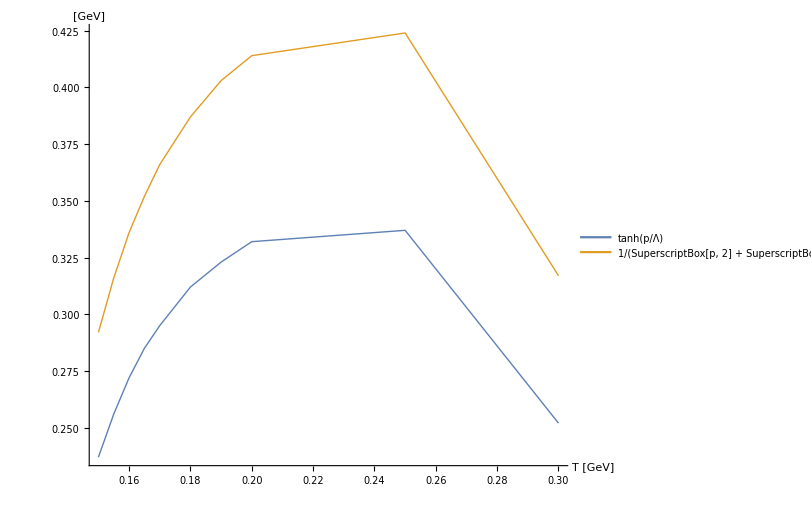

```mathematica
ListPlot[{Transpose[{Tset,regARre}],Transpose[{Tset,regre}]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","[GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True,PlotStyle->Thick,PlotLegends->Placed[{"tanh(p/Λ)","1/(SuperscriptBox[p, 2] + SuperscriptBox[Λ, 2])^(1/2)"},{0.5,0.2}]]
```

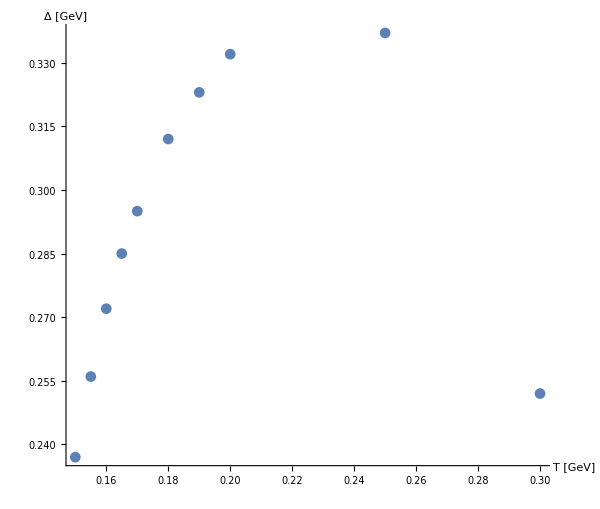

```mathematica
ImVsARAll[n1_]:=Block[{n=n1,temp},temp=ImVsARTab[mDcal[2π,Tset[[n]],kfinal[[1]],kfinal[[2]]],regARre[[n]],σcont[[1]],Tset[[n]]];
Export["reg_pot/ImVsART"<>ToString[n]<>".dat",temp];
ImVsARInter[n]=Interpolation[temp];]
```

```mathematica
ImVsARAll[1]
ImVsARAll[2]
ImVsARAll[3]
ImVsARAll[4]
ImVsARAll[5]
ImVsARAll[6]
ImVsARAll[7]
ImVsARAll[8]
ImVsARAll[9]
ImVsARAll[10]
```

```mathematica
Plot[{ImVsARInter[1][x/conv],ImVsARInter[2][x/conv],ImVsARInter[3][x/conv],ImVsARInter[4][x/conv],ImVsARInter[5][x/conv],ImVsARInter[6][x/conv],ImVsARInter[7][x/conv],ImVsARInter[8][x/conv],ImVsARInter[9][x/conv]},{x,0,10},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TsetSnew, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.7,0.4}]]
```

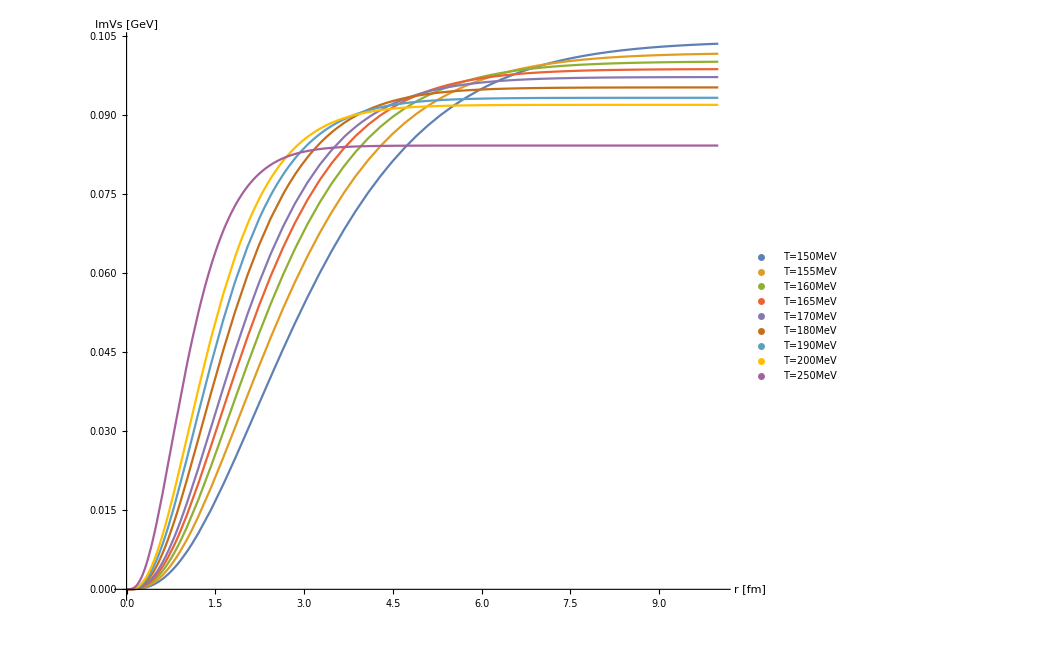
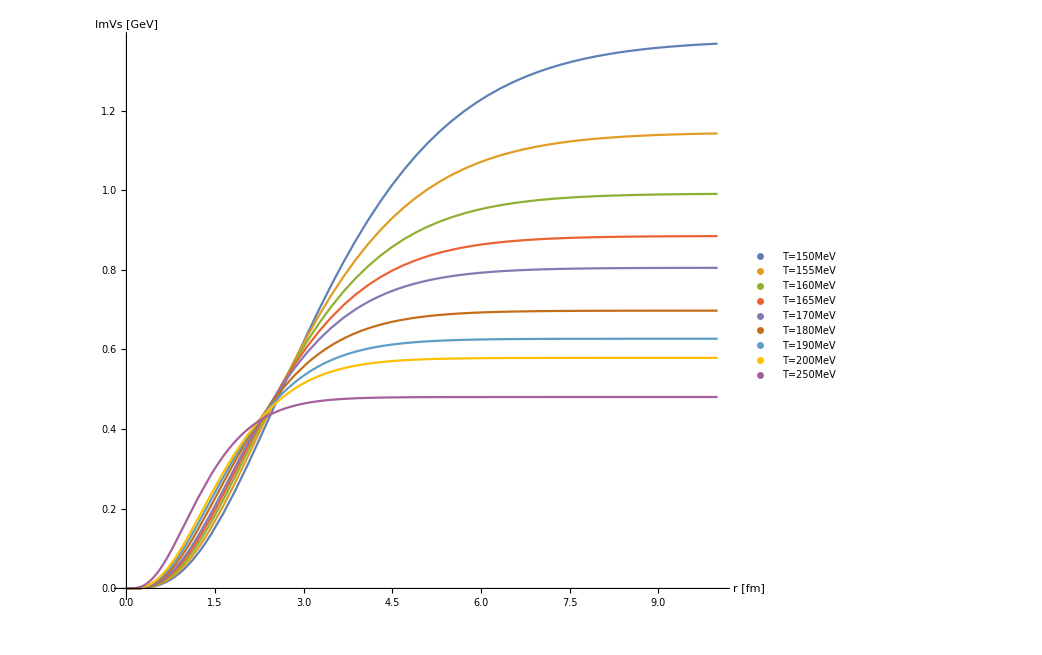

## Plots for lattice fits

```mathematica
Tlat=SetPrecision[{0.1478,0.1642,0.1818,0.2054,0.2317,0.2425,0.2861},30];
αlat=SetPrecision[{0.4859592638209618,0.47104500698378393,0.4561307501466063,0.4374879291001341,0.41884510805366193,0.411387979635073,0.384542317328153},30];
σlat=SetPrecision[{0.2088434405704896,0.21706585496978287,0.22528826936907603,0.23556628736819257,0.245844305367309,0.24995551256695564,0.26475585848568345},30];
clat=SetPrecision[{1.6313652574133624,1.7808011444057126,1.9302370313980628,2.117031890138499,2.303826748878935,2.37854469237511,2.6475292889613407},30];
mdlat=SetPrecision[{0.06997549222118046,0.18764366844838265,0.25469933582761983,0.3734921779850663,0.5267111789784007,0.5405169214400376,0.6676534051261366},30];
```

```mathematica
TlatS={"T=148MeV","T=164MeV","T=182MeV","T=205MeV","T=232MeV","T=243MeV","T=286MeV"};
```

```mathematica
ReVlatplot=Table[ReV[r/conv,mdlat[[l]],αlat[[l]],σlat[[l]],clat[[l]]]-clat[[l]],{l,1,7}];
```

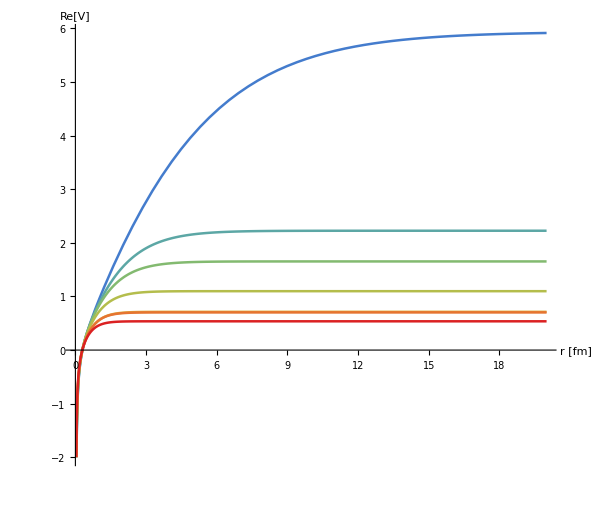

```mathematica
ReVlatanPlot=Plot[ReVlatplot,{r,0.001,20},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.8,0.95}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{600,600}]
```

```mathematica
ReVlatas[n_]:=clat[[n]]-αlat[[n]]mdlat[[n]]+(2 σlat[[n]])/mdlat[[n]];
```

```mathematica
rsbthlat=SetPrecision[Table[{Tlat[[n]],r/.FindRoot[ReV[r/conv,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.99ReVlatas[n],{r,1/10,1/100,30}]},{n,1,7}],30];
```

```mathematica
rsb9thlat=SetPrecision[Table[{Tlat[[n]],r/.FindRoot[ReV[r/conv,mdlat[[n]],αlat[[n]],σlat[[n]],clat[[n]]]==0.999ReVlatas[n],{r,1/10,1/100,30}]},{n,1,7}],30];
```

```mathematica
mdlatinv=SetPrecision[Table[{Tlat[[n]],conv/mdlat[[n]]},{n,1,7}],30];
```

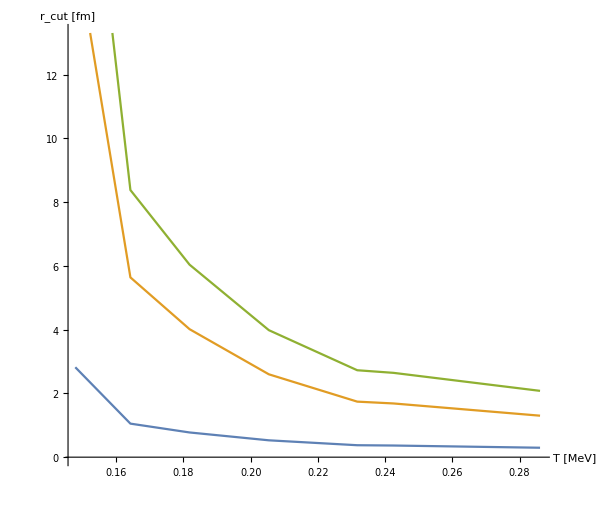

```mathematica
ListPlot[{mdlatinv,rsbthlat,rsb9thlat},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [MeV]","r_cut [fm]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

```mathematica
ImVclatplot=Table[ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]],{l,1,7}];
```

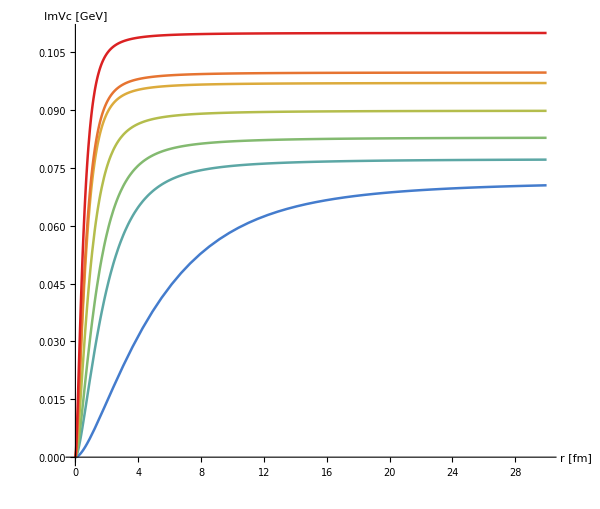

```mathematica
ImVclatanPlot=Plot[ImVclatplot,{r,0.001,30},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{600,600}]
```

```mathematica
ImVslatplot=ParallelTable[ImVs[r/conv,mdlat[[l]],σlat[[l]],Tlat[[l]]],{l,1,7}];
```

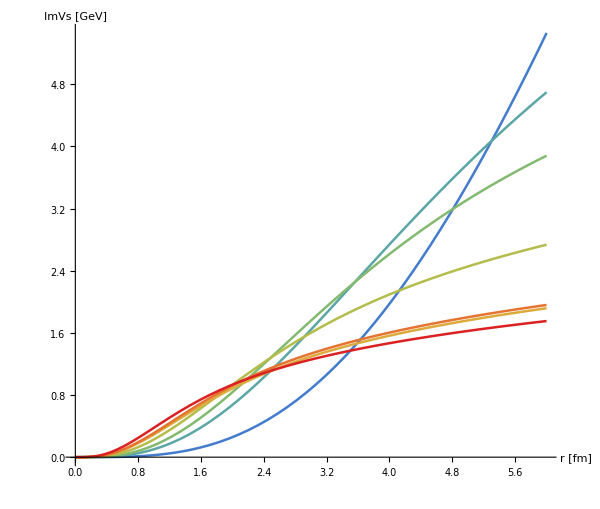

```mathematica
ImVslatanPlot=Plot[ImVslatplot,{r,0.001,6},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{600,600}]
```

```mathematica
ImVssblatplot=ParallelTable[ImVssb[r/conv,mdlat[[l]],σlat[[l]],Tlat[[l]],rsb9thlat[[l,2]]/conv],{l,1,7}];
```

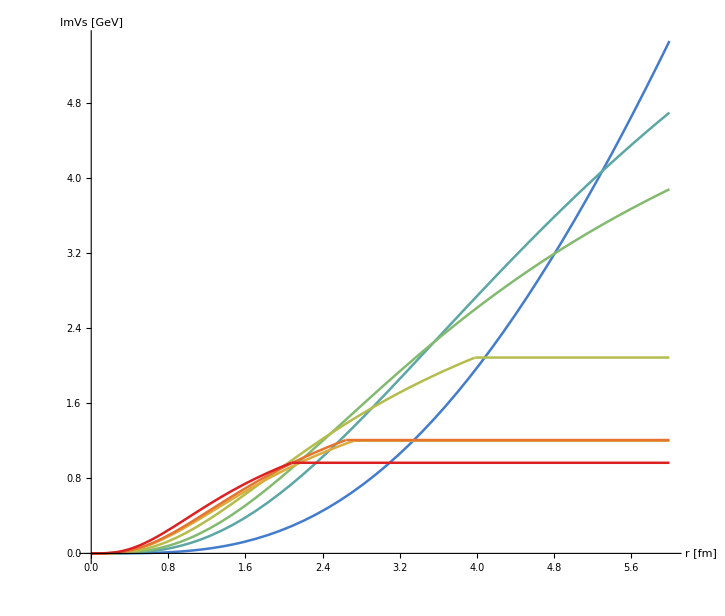

```mathematica
ImVssblatanPlot=Plot[ImVssblatplot,{r,0.001,6},PlotStyle->Thread@{AbsoluteThickness[1.8],ColorData["Rainbow"]/@Range[2/8,1,1/8]},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.5,0.5}],BaseStyle->{FontSize->14},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{600,600}]
```

### Regularisation

#### Decorrelation length via real part

```mathematica
reglat=ConstantArray[1/1000,Length[rsb9thlat]];
SetSharedVariable[reglat];
ParallelDo[While[ImVsr[rsb9thlat[[l,2]]/conv,mdlat[[l]],reglat[[l]],σlat[[l]],Tlat[[l]]]/ImVsAs[mdlat[[l]],reglat[[l]],σlat[[l]],Tlat[[l]]]<90/100,reglat[[l]]=reglat[[l]]+1/100],{l,Length[reglat]}];
```

```mathematica
N[reglat]
```

{0.031,0.081,0.121,0.181,0.281,0.291,0.391}

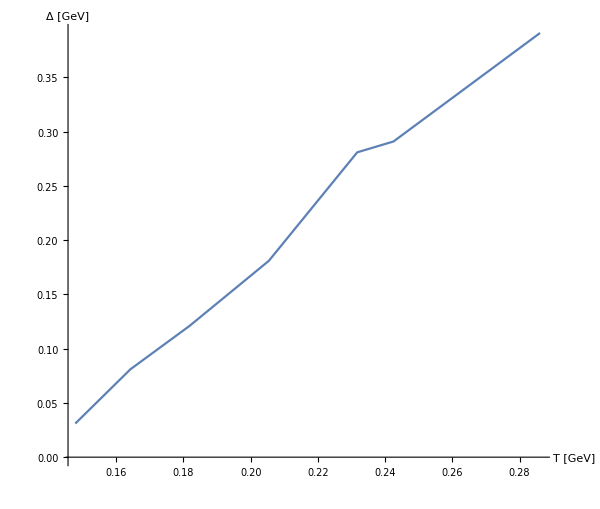

```mathematica
ListPlot[Transpose[{Tlat,reglat}],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Δ [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14},Joined->True]
```

```mathematica
ImVsAll[n1_]:=Block[{n=n1,temp},temp=ImVsTab[mdlat[[n]],reglat[[n]],σlat[[n]],Tlat[[n]]];
Export["reg_pot/ImVslatT"<>ToString[n]<>".dat",temp];
ImVsInter[n]=Interpolation[temp];]
```

```mathematica
ImVsAll[1]//AbsoluteTiming
```

{275.954,Null}

```mathematica
ImVsAll[2]//AbsoluteTiming
```

{282.589,Null}

```mathematica
ImVsAll[3]//AbsoluteTiming
```

{345.802,Null}

```mathematica
ImVsAll[4]//AbsoluteTiming
```

{375.185,Null}

```mathematica
ImVsAll[5]//AbsoluteTiming
```

{371.347,Null}

```mathematica
ImVsAll[6]//AbsoluteTiming
```

{362.044,Null}

```mathematica
ImVsAll[7]//AbsoluteTiming
```

{370.184,Null}

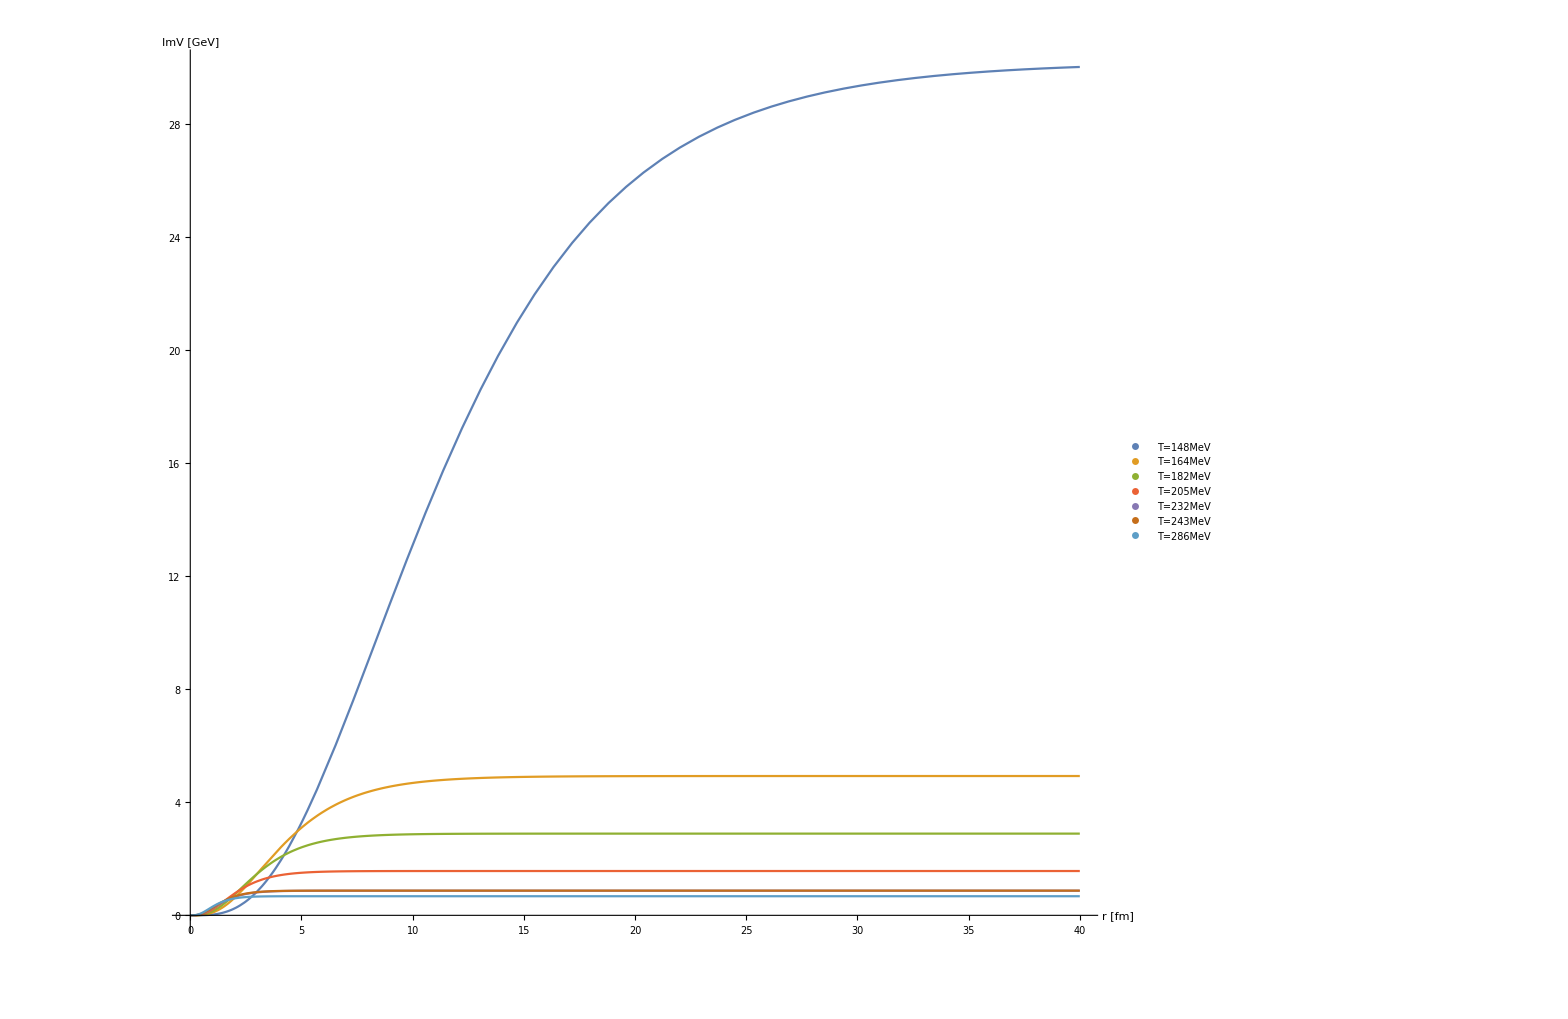

```mathematica
Plot[{ImVsInter[1][x/conv],ImVsInter[2][x/conv],ImVsInter[3][x/conv],ImVsInter[4][x/conv],ImVsInter[5][x/conv],ImVsInter[6][x/conv],ImVsInter[7][x/conv]},{x,0,40},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImV [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.6,0.7}],PlotRange->All]
```

#### Via hyperbolic tangent

```mathematica
ImVsARTab[mD1_,Δ1_,σ1_,T1_]:=Block[{mD=mD1,Δ=Δ1,σ=σ1,T=T1},Join[{{0,0}},ParallelTable[{r,NIntegrate[(2 mD^2 T σ (2-2 Cos[p r]-p r Sin[p r]))/(p(mD^2+p^2)^2)Tanh[Δ^-1 p],{p,0,∞}]},{r,1/100,100,1/100}]]];
```

```mathematica
ImVsARAs[mD_,Δ_,σ_,T_]:=4 mD^2 T σ NIntegrate[1/(p(mD^2+p^2)^2)Tanh[Δ^-1 p],{p,0,∞},WorkingPrecision->20,MaxRecursion->20];
```

```mathematica
N[rsb9thlat]
```

{{0.1478,23.436},{0.1642,8.3768},{0.1818,6.0369},{0.2054,3.98248},{0.2317,2.7259},{0.2425,2.64391},{0.2861,2.07953}}

```mathematica
regARlatre=ConstantArray[1/1000,Length[rsb9thlat]];
SetSharedVariable[regARlatre];
ParallelDo[While[ImVsrAR[rsb9thlat[[l,2]]/conv,mdlat[[l]],regARlatre[[l]],σlat[[l]],Tlat[[l]]]/ImVsARAs[mdlat[[l]],regARlatre[[l]],σlat[[l]],Tlat[[l]]]<990/1000,regARlatre[[l]]=regARlatre[[l]]+1/1000],{l,Length[regARlatre]}];
```

```mathematica
N[regARlatre]
```

{1.001,1.003,1.004,1.006,1.01,1.011,1.015}

```mathematica
regARlatre={1.001,1.003,1.004,1.006,1.01,1.011,1.015};
```

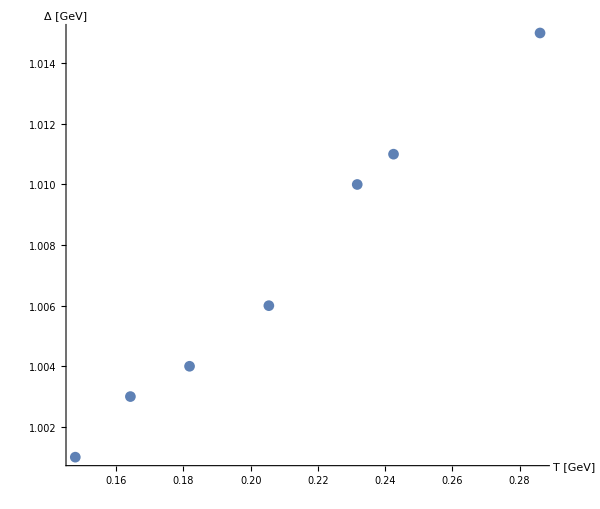

```mathematica
ListPlot[Transpose[{Tlat,regARlatre}],AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"T [GeV]","Δ [GeV]"},ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

```mathematica
ImVsARAll[n1_]:=Block[{n=n1,temp},temp=ImVsARTab[mdlat[[n]],regARlatre[[n]],σlat[[n]],Tlat[[n]]];
Export["reg_pot/ImVsARlatT"<>ToString[n]<>".dat",temp];
ImVsARlatInter[n]=Interpolation[temp];]
```

```mathematica
ImVsARAll[1]
ImVsARAll[2]
ImVsARAll[3]
ImVsARAll[4]
ImVsARAll[5]
ImVsARAll[6]
```

```mathematica
ImVsARAll[7]
```

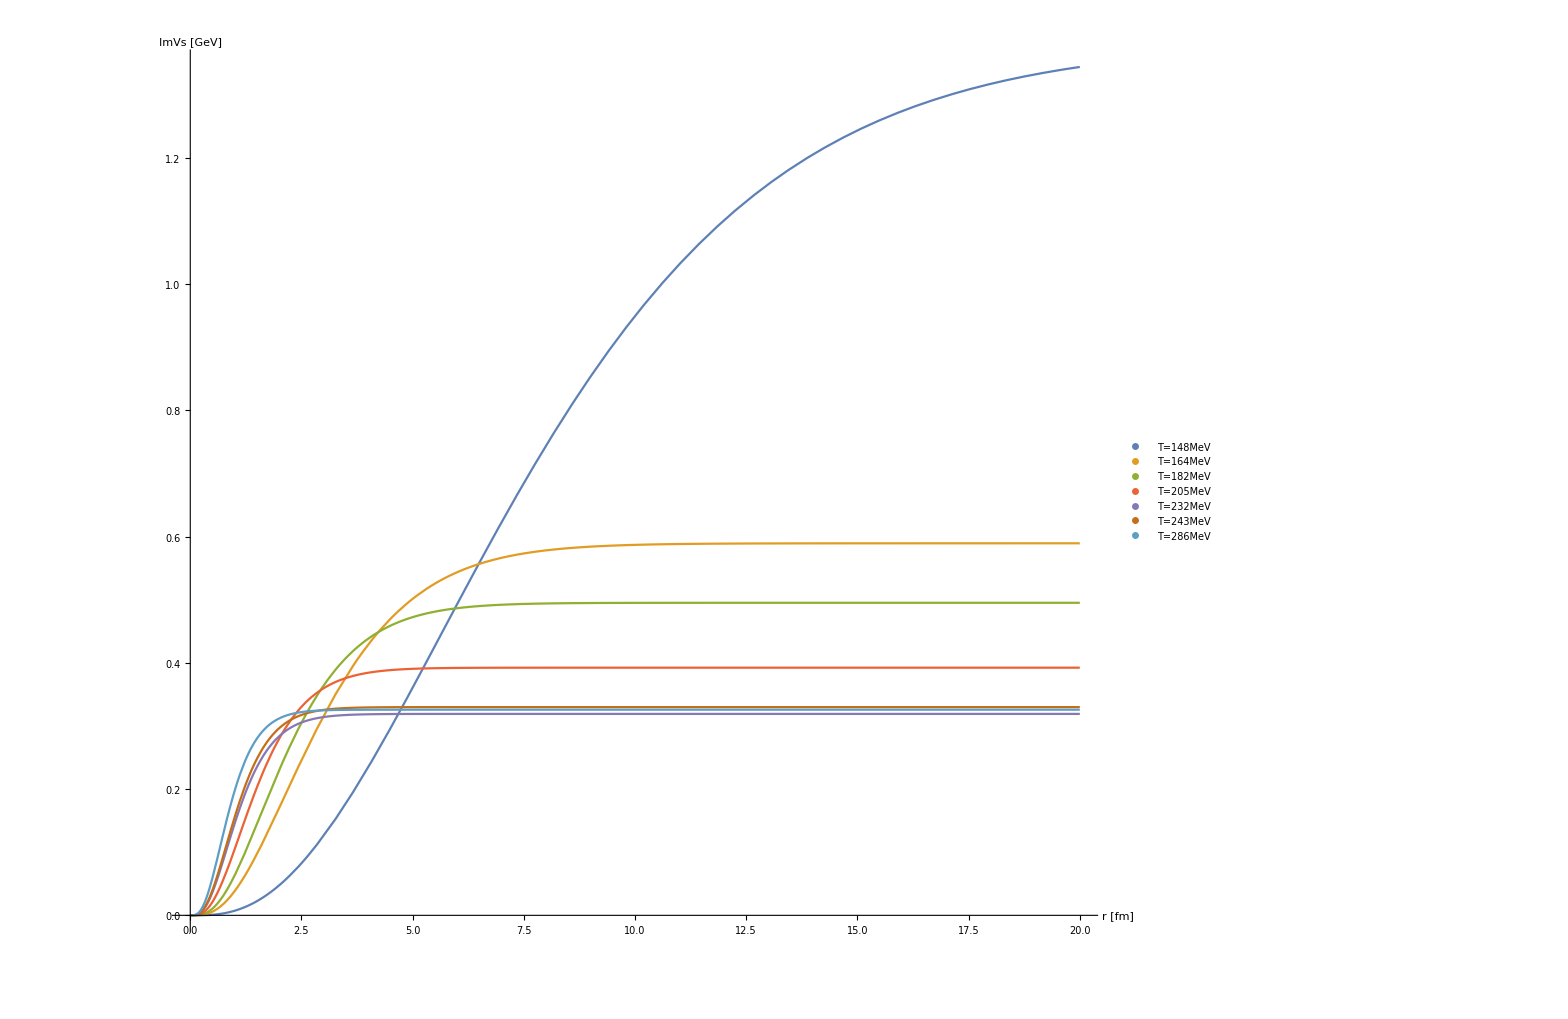

```mathematica
Plot[{ImVsARlatInter[1][x/conv],ImVsARlatInter[2][x/conv],ImVsARlatInter[3][x/conv],ImVsARlatInter[4][x/conv],ImVsARlatInter[5][x/conv],ImVsARlatInter[6][x/conv],ImVsARlatInter[7][x/conv]},{x,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1200,1200},PlotLegends->Placed[PointLegend[TlatS, LegendMarkerSize->15,LegendLayout->{"Row",3}],{0.3,0.7}],PlotRange->All]
```

### Include lattice data

```mathematica
Needs["ErrorBarPlots`"];
Vdata=SplitBy[Import["../latticedata/AllData2p1Flavors/Vall.txt","Table"],First];

ImVdataT[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTe[n_]:=Table[{Vdata[[n,x,2]],Vdata[[n,x,5]],Vdata[[n,x,6]]},{x,1,Dimensions[Vdata[[n]]][[1]]}];
ImVdataTn[n_]:=ImVdataT[n]/.{a_,b_}:>{a/0.197327,b};
ImVdataTne[n_]:=ImVdataTe[n]/.{a_,b_,c_}:>{a/0.197327,b,c};
```

```mathematica
Shift=1.
```

1.

```mathematica
For[l=1,l≤ 7,l++,PotImRescale[l]=ImVdataTe[l]/.{a_,b_,c_}:>{a-Shift*l+7*Shift,b,c}];
```

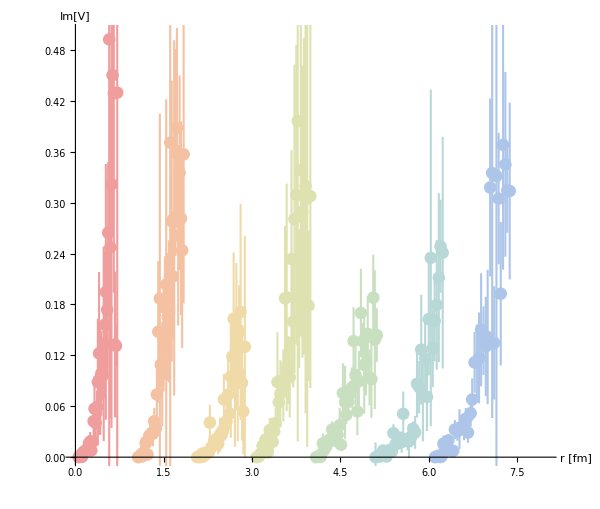

```mathematica
ImVdatPlot=ErrorListPlot[Table[PotImRescale[l][[1;;Floor[Length[PotImRescale[l]]*0.9]]],{l,1,7}],PlotRange->{{0,8},{0,0.5}},PlotStyle->Thread@{AbsolutePointSize[9],AbsoluteThickness[1.5],Lighter[Lighter[ColorData["Rainbow"]/@Range[2/8,1,1/8]]]},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->16},AspectRatio->0.85,PlotRange->{0,0.35},AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

#### Decorrelation length via real part

```mathematica
ImVtab[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[1][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,2,1/100}]];
ImVtab[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[2][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,3,1/100}]];
ImVtab[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[3][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,4,1/100}]];
ImVtab[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[4][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,5,1/100}]];
ImVtab[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[5][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,6,1/100}]];
ImVtab[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[6][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,7,1/100}]];
ImVtab[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInter[7][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,8,1/100}]];
```

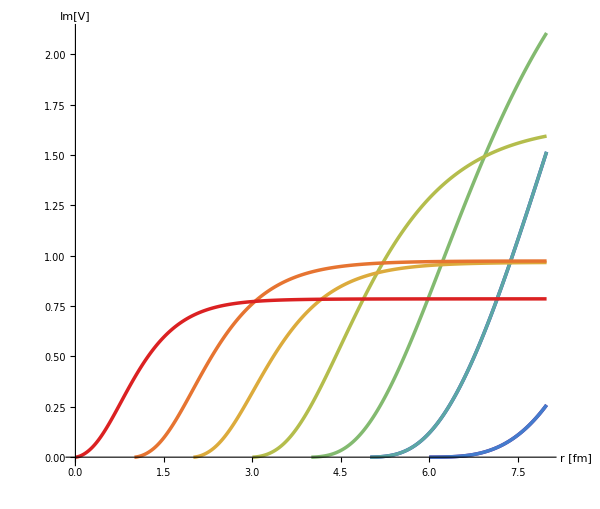

```mathematica
ImVPlot=ListPlot[{ImVtab[1,0],ImVtab[2,0],ImVtab[1,0],ImVtab[2,0],ImVtab[3,0],ImVtab[4,0],ImVtab[5,0],ImVtab[6,0],ImVtab[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

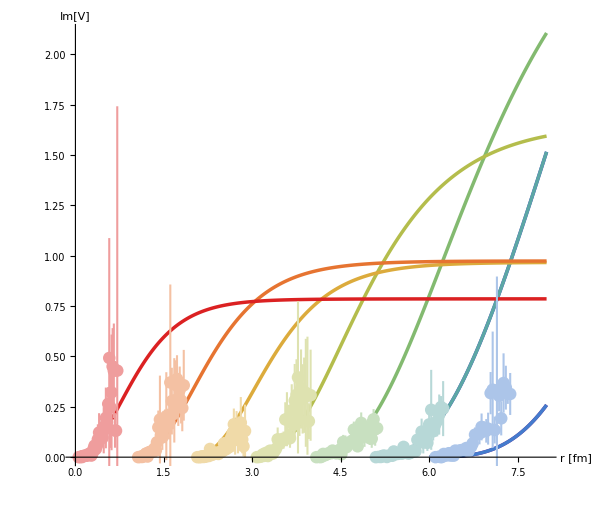

```mathematica
Show[ImVPlot,ImVdatPlot]
```

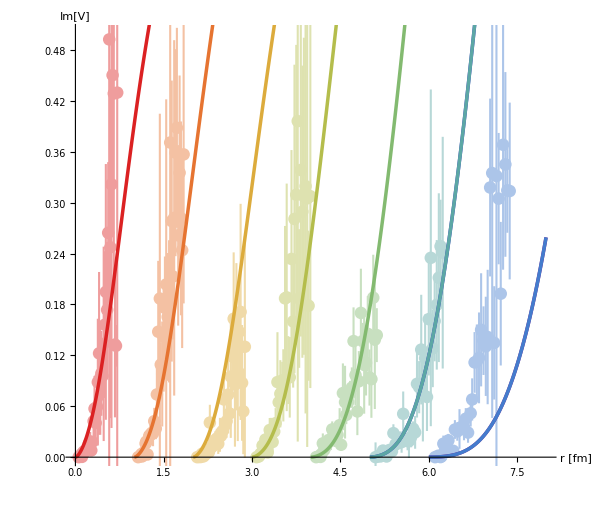

```mathematica
Show[ImVdatPlot,ImVPlot]
```

#### Via hyperbolic tangent

```mathematica
ImVsInterAR[1]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT1.dat"]]];
ImVsInterAR[2]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT2.dat"]]];
ImVsInterAR[3]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT3.dat"]]];
ImVsInterAR[4]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT4.dat"]]];
ImVsInterAR[5]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT5.dat"]]];
ImVsInterAR[6]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT6.dat"]]];
ImVsInterAR[7]=Interpolation[ToExpression[Import["reg_pot/ImVsARlatT7.dat"]]];
```

```mathematica
ImVeAR[1,0]=Block[{l=1,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[1][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,2,1/100}]];
ImVeAR[2,0]=Block[{l=2,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[2][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,3,1/100}]];
ImVeAR[3,0]=Block[{l=3,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[3][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,4,1/100}]];
ImVeAR[4,0]=Block[{l=4,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[4][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,5,1/100}]];
ImVeAR[5,0]=Block[{l=5,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[5][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,6,1/100}]];
ImVeAR[6,0]=Block[{l=6,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[6][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,7,1/100}]];
ImVeAR[7,0]=Block[{l=7,a=0},ParallelTable[{r-Shift*l+7*Shift,ImVsInterAR[7][r/conv]+ImVc[r/conv,mdlat[[l]],αlat[[l]],Tlat[[l]]]},{r,1/1000,8,1/100}]];
```

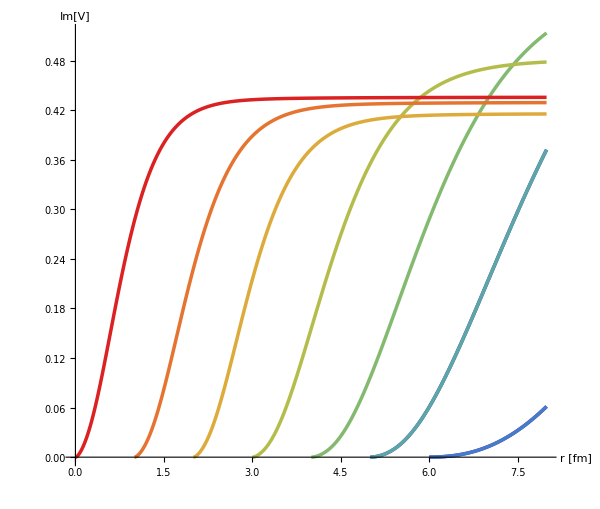

```mathematica
ImVPlotAR=ListPlot[{ImVeAR[1,0],ImVeAR[2,0],ImVeAR[1,0],ImVeAR[2,0],ImVeAR[3,0],ImVeAR[4,0],ImVeAR[5,0],ImVeAR[6,0],ImVeAR[7,0]},Joined->True,PlotStyle->{{RGBColor[0.471412, 0.108766, 0.527016],AbsoluteThickness[2.5]},{RGBColor[0.250728, 0.225386, 0.769152],AbsoluteThickness[2.5]},{RGBColor[0.266122, 0.486664, 0.802529],AbsoluteThickness[2.5]},{RGBColor[0.36048, 0.655759, 0.645692],AbsoluteThickness[2.5]},{RGBColor[0.513417, 0.72992, 0.440682],AbsoluteThickness[2.5]},{RGBColor[0.705038, 0.742591, 0.299167],AbsoluteThickness[2.5]},{RGBColor[0.863512, 0.670771, 0.236564],AbsoluteThickness[2.5]},{RGBColor[0.902853, 0.453964, 0.192014],AbsoluteThickness[2.5]},{RGBColor[0.857359, 0.131106, 0.132128],AbsoluteThickness[2.5]}},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},ImageSize->{600,600}]
```

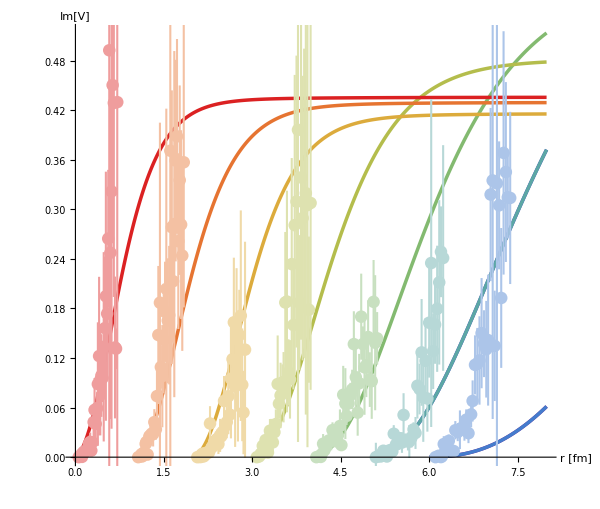

```mathematica
Show[ImVPlotAR,ImVdatPlot]
```

```mathematica
Show[ImVdatPlot,ImVPlotAR]
```